# Структурно-сетевые методы моделирования стратегий борьбы с распространением эпидемии

## Мухамадиев В.И.

## Введение

Такие меры как самоизоляция, карантин, отслеживание первичных контактов, тестирование способствуют борьбе с эпидемиями. Однако не понятно насколько эффективна та или иная мера. Ответить на этот вопрос возможно при помощи моделирования распространения эпидемии с учетом данных стратегий. Для этого необходима реальная социальная сеть в которой известно расстояние между вершинами и данная сеть не должна быть статичной, она должна изменяться во времени. В данном исследовании была рассмотрена база данных социальных контактов Хейзлмира [1]. Хейзлмир - небольшой город на юге Англии с населением 11235 человек по данным переписи населения Великобритании 2011 года [2]. Данный город был выбран для сбора данных по социальным контактам по причине его размера и расположения. Хейзлмир является транзитным городом между Лондоном и Портсмутом. Данное местоположение делает его вероятным местом возникновения вспышки. Размер города гарантирует, что в нем есть типичные объекты инфраструктуры: железнодорожная станция, магазины, школы.

#### Карта Великобритании с местоположением Хейзлмира

```mathematica
GeoListPlot[{Entity["Country","UnitedKingdom"],Entity["City",{"London","GreaterLondon","UnitedKingdom"}],Entity["City",{"Haslemere","Surrey","UnitedKingdom"}]},GeoLabels->Automatic,
ImageSize->Large]
```

-Graphics-

Участники исследования загружали приложение на свои смартфоны и с помощью него отправляли свои GPS-координаты. Данные записывались в течение трех дней подряд. Далее были отброшены все местоположения за пределами города. Полученные данные были сгруппированы по пятиминутным интервалам, а расстояния округлены с точностью до метра. Данные представлены в виде двух файлов. В первом файле каждая строка представляет собой встречу (в пределах 50 м) между двумя пользователями. Первый столбец - шаг по времени в виде целого числа. В столбцах 2 и 3 указаны идентификационные номера пользователей. В столбце 4 указано расстояние между пользователями на данном временном шаге, округленное до ближайшего метра. Во втором файле стоит соответствие шага по времени из первого столбца между индексами времени в реальное время по британскому стандартному времени (BST). Всего у нас 576 временных отсечек и 469 пользователей (вершин).

## Обработка данных

Загружаем данные из репозитория.

```mathematica
KDS1=Import["https://raw.githubusercontent.com/skissler/haslemere/master/Kissler_DataS1.csv"];
(*KDS1=Import[FileNameJoin[{NotebookDirectory[],"Kissler_DataS1.csv"}],"CSV"];*)
KDS2=Import["https://raw.githubusercontent.com/skissler/haslemere/master/Kissler_DataS2.csv"];
(*KDS2=Import[FileNameJoin[{NotebookDirectory[],"Kissler_DataS2.csv"}],"CSV"];*)
```

Приводим  KisslerDataS1 к виду {{{1,...,...,...},{1,...,...,...},...},{{2,...,...,...},{2,...,...,...},...},...,{{576,...,...,...},{576,...,...,...},...}} получая таким образом последовательность из списков где каждый список представляет собой состояние сети в определенный момент времени.

```mathematica
datasep=Table[Cases[KDS1,{i,_,_,_}],{i,1,Length[KDS2]}];
```

Предполагая, что вероятность заражения падает экспоненциально с расстоянием [3], мы в дальнейшем введем коэффициент равный обратной экспоненте от расстояния. Из этого предположения мы получаем что при расстоянии 5 метров, вероятность заражения будет менее 1%. По этой причине в дальнейшем для снижения временных затрат при моделировании есть смысл рассмотреть сеть, в которой убраны все контакты с расстоянием более 5 метров. Отфильтруем наши данные убрав ребра, в которых расстояние превышает 5 метров. Здесь и далее переменные оканчивающиеся на "5m" означают, что они относятся к сети в который остались только ребра с расстоянием не более 5 метров.

```mathematica
datasep5m=Table[Cases[datasep⟦i⟧,{_,_,_,x_Integer}/;x≤5],{i,1,Length[datasep]}];
```

Теперь нам необходимо создать для каждого временного состояния список ребер.

```mathematica
edgelist=Table[Table[datasep⟦j,i,2⟧<->datasep⟦j,i,3⟧,{i,1,Length[datasep⟦j⟧]}],
{j,1,Length[datasep]}];
edgelist5m=Table[Table[datasep5m⟦j,i,2⟧<->datasep5m⟦j,i,3⟧,{i,1,Length[datasep5m⟦j⟧]}],
{j,1,Length[datasep5m]}];
```

Так как в нашей сети у ребер есть расстояния, то нам необходимо так же создать списки с расстояниями.

```mathematica
edgelength=Table[Table[N[datasep⟦j,i,4⟧],{i,1,Length[datasep⟦j⟧]}],
{j,1,Length[datasep]}];
edgelength5m=Table[Table[N[datasep5m⟦j,i,4⟧],{i,1,Length[datasep5m⟦j⟧]}],
{j,1,Length[datasep5m]}];
```

Предположим, что вероятность заразиться от человека с которым был прямой контакт в течение 1 часа ≥95%. В 1 часе содержится 12 пятиминутных интервалов. Посчитаем данную вероятность.

```mathematica
p=Solve[1-(1-v)^12==0.95&&0<v<1,v]⟦1,1,2⟧
```

0.220922

Введем коэффициент (вес ребра) равный обратной экспоненте от расстояния помноженный на p, по которому будет считаться вероятность заражения.

```mathematica
w=p ⅇ^-edgelength;
w5m=p ⅇ^-edgelength5m;
```

#### График обратной экспоненты

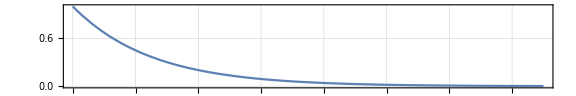

```mathematica
Plot[ⅇ^-x,{x,0,6},PlotRange->{{0,6},{0,1}},AspectRatio->1/6,PlotTheme->"Detailed",ImageSize->Large]
```

Таким образом для каждой временной отсечки у нас есть список ребер и их веса. Теперь мы можем создать состояние графа для каждой временной отсечки. Убедимся что в нашей сети 469 вершин.

```mathematica
vertexcount=Length[DeleteDuplicates[Flatten[KDS1⟦All,2;;3⟧]]]
```

469

Создадим сетку с вершинами для дальнейшей визуализации.

```mathematica
grid=Partition[Flatten[Table[{i,j},{i,1,Ceiling[√vertexcount]},
{j,1,Ceiling[√vertexcount]}]],2]⟦1;;vertexcount⟧;
```

Создаем сеть изменяемую во времени.

```mathematica
network=Table[EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],edgelist⟦i⟧,
VertexCoordinates->Table[i->grid⟦i⟧,{i,1,vertexcount}],
EdgeStyle->Table[edgelist⟦i,j⟧->Thickness[0.01 w⟦i,j⟧/p],{j,1,Length[edgelist⟦i⟧]}],
ImageSize->Large],{i,1,Length[edgelist]}];
network5m=Table[EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],edgelist5m⟦i⟧,
VertexCoordinates->Table[i->grid⟦i⟧,{i,1,vertexcount}],
EdgeStyle->Table[edgelist5m⟦i,j⟧->Thickness[0.01 w5m⟦i,j⟧/p],{j,1,Length[edgelist5m⟦i⟧]}],
ImageSize->Large],{i,1,Length[edgelist5m]}];
```

## Исследование сети

Визуализируем полученную сеть расположив вершины в виде квадратной решетки. Чем больше толщина ребра, тем меньше расстояние между вершинами.

```mathematica
nv=Table[Grid[{{KDS2⟦i,2⟧},{network⟦i⟧}}],{i,1,Length[KDS2]}];
nv5m=Table[Grid[{{KDS2⟦i,2⟧},{network5m⟦i⟧}}],{i,1,Length[KDS2]}];
```

#### Пример визуализации для графа со всеми расстояниями

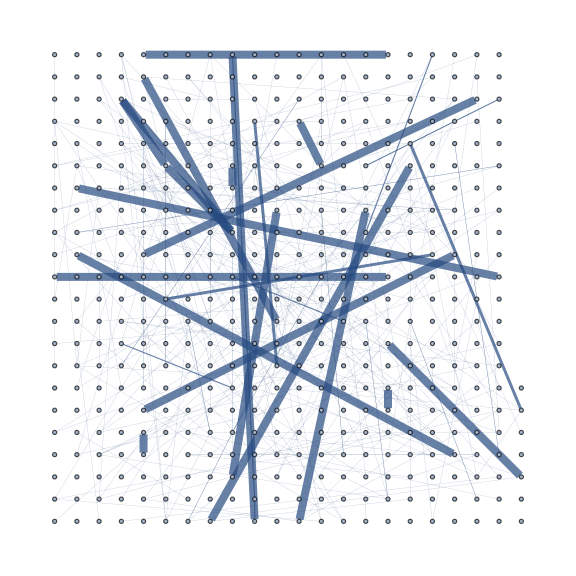
Thu 12 Oct 2017 07:00:00
-Graphics-

```mathematica
nv⟦1⟧
```

#### Визуализация этой же временной отсечки, но отброшены ребра с расстоянием более 5 метров

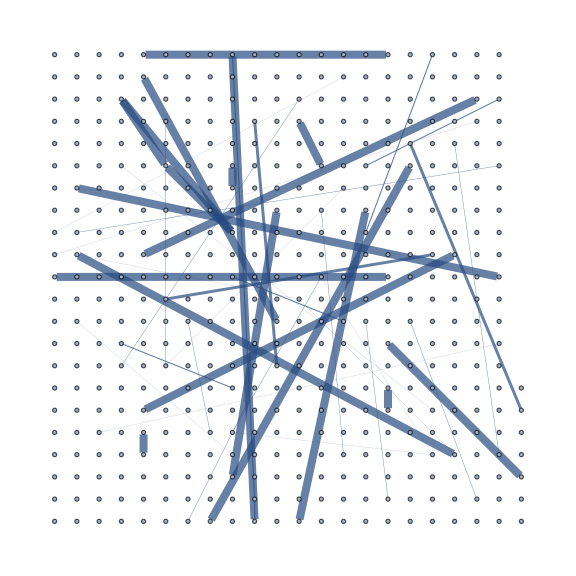
Thu 12 Oct 2017 07:00:00
-Graphics-

```mathematica
nv5m⟦1⟧
```

Рассмотрим изменение различных характеристик сети во времени.

#### Динамика изменения числа ребер сети во времени

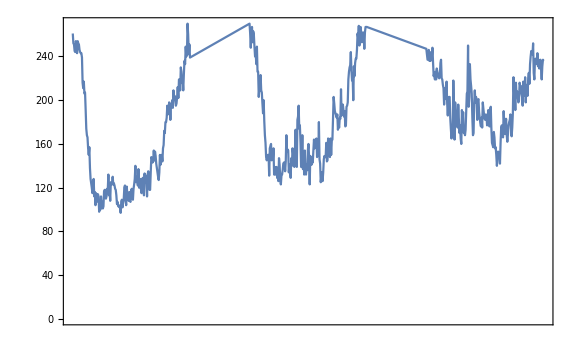

```mathematica
DateListPlot[TimeSeries[Table[EdgeCount[network⟦i⟧],{i,1,Length[network]}],
{KDS2⟦All,2⟧}],FrameTicks->{{Automatic,Automatic},{{"Thu 12 Oct 2017 07:00:00",
"Thu 12 Oct 2017 11:00:00","Thu 12 Oct 2017 15:00:00","Thu 12 Oct 2017 19:00:00",
"Thu 12 Oct 2017 23:00:00","Fri 13 Oct 2017 07:00:00","Fri 13 Oct 2017 11:00:00",
"Fri 13 Oct 2017 15:00:00","Fri 13 Oct 2017 19:00:00","Fri 13 Oct 2017 23:00:00",
"Sat 14 Oct 2017 07:00:00","Sat 14 Oct 2017 11:00:00","Sat 14 Oct 2017 15:00:00",
"Sat 14 Oct 2017 19:00:00","Sat 14 Oct 2017 23:00:00"},Automatic}},
DateTicksFormat->{"MonthNameShort"," ","Day","\n","Hour24Short",":00"},ImageSize->Large]
```

#### Наложение по дням

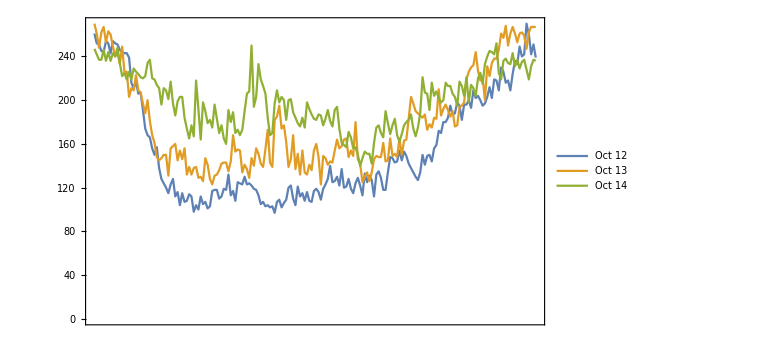

```mathematica
DateListPlot[{TimeSeries[Table[EdgeCount[network⟦i⟧],{i,1,192}],
{Flatten[Table[StringCases[KDS2⟦i,2⟧,RegularExpression["..:..:.."]],{i,1,192}]]}],
TimeSeries[Table[EdgeCount[network⟦i⟧],{i,193,384}],
{Flatten[Table[StringCases[KDS2⟦i,2⟧,RegularExpression["..:..:.."]],{i,1,192}]]}],
TimeSeries[Table[EdgeCount[network⟦i⟧],{i,385,576}],
{Flatten[Table[StringCases[KDS2⟦i,2⟧,RegularExpression["..:..:.."]],{i,1,192}]]}]},
PlotLegends->{"Oct 12","Oct 13","Oct 14"},ImageSize->Large]
```

В течении каждого дня мы можем наблюдать тенденцию снижения числа связей (ребер) к середине дня и рост числа связей к его окончанию. Среднее количество ребер в сети:

```mathematica
N[Mean[Table[EdgeCount[network⟦i⟧],{i,1,Length[network]}]]]
```

178.526

Так как плотность и средняя степень вершины напрямую зависят от количества ребер то их графики будут иметь такой же вид. Так что приведем только их средние значения. Плотность:

```mathematica
N[Mean[Table[GraphDensity[network⟦i⟧],{i,1,Length[network]}]]]
```

0.00162672

Средняя степень вершины:

```mathematica
N[Mean[Table[Mean[VertexDegree[network⟦i⟧]],{i,1,Length[network]}]]]
```

0.761305

Ассортативность сети не зависит напрямую от числа ребер. Рассмотрим динамику её изменения во времени.

#### Динамика изменения ассортативности сети во времени

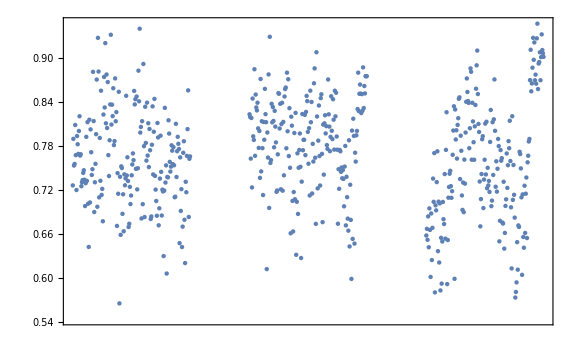

```mathematica
DateListPlot[TimeSeries[Table[GraphAssortativity[network⟦i⟧],{i,1,Length[network]}],
{KDS2⟦All,2⟧}],FrameTicks->{{Automatic,Automatic},{{"Thu 12 Oct 2017 07:00:00",
"Thu 12 Oct 2017 11:00:00","Thu 12 Oct 2017 15:00:00","Thu 12 Oct 2017 19:00:00",
"Thu 12 Oct 2017 23:00:00","Fri 13 Oct 2017 07:00:00","Fri 13 Oct 2017 11:00:00",
"Fri 13 Oct 2017 15:00:00","Fri 13 Oct 2017 19:00:00","Fri 13 Oct 2017 23:00:00",
"Sat 14 Oct 2017 07:00:00","Sat 14 Oct 2017 11:00:00","Sat 14 Oct 2017 15:00:00",
"Sat 14 Oct 2017 19:00:00","Sat 14 Oct 2017 23:00:00"},Automatic}},
DateTicksFormat->{"MonthNameShort"," ","Day","\n","Hour24Short",":00"},Joined->False,ImageSize->Large]
```

Как мы видим зависимости ассортативности сети от времени суток не наблюдается, но при этом на протяжении всех трёх дней наблюдений ассортативность оставалась на высоком уровне что характерно для социальных сетей [4] так же как и низкая плотность [5]. Среднее значение ассортативности:

```mathematica
N[Mean[Table[GraphAssortativity[network⟦i⟧],{i,1,Length[network]}]]]
```

0.767812

Из характеристик сети так же интересно рассмотреть динамику изменения глобального коэффициента кластеризации.

#### Динамика изменения глобального коэффициента кластеризации сети во времени

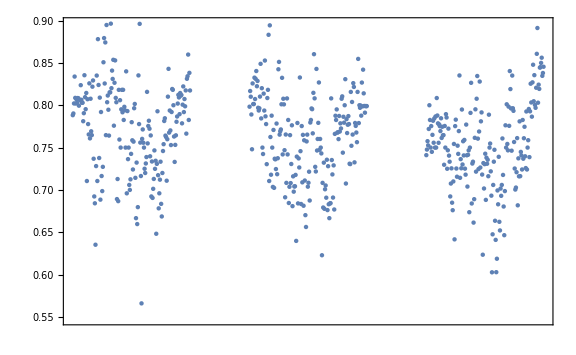

```mathematica
DateListPlot[TimeSeries[Table[GlobalClusteringCoefficient[network⟦i⟧],{i,1,Length[network]}],
{KDS2⟦All,2⟧}],FrameTicks->{{Automatic,Automatic},{{"Thu 12 Oct 2017 07:00:00",
"Thu 12 Oct 2017 11:00:00","Thu 12 Oct 2017 15:00:00","Thu 12 Oct 2017 19:00:00",
"Thu 12 Oct 2017 23:00:00","Fri 13 Oct 2017 07:00:00","Fri 13 Oct 2017 11:00:00",
"Fri 13 Oct 2017 15:00:00","Fri 13 Oct 2017 19:00:00","Fri 13 Oct 2017 23:00:00",
"Sat 14 Oct 2017 07:00:00","Sat 14 Oct 2017 11:00:00","Sat 14 Oct 2017 15:00:00",
"Sat 14 Oct 2017 19:00:00","Sat 14 Oct 2017 23:00:00"},Automatic}},
DateTicksFormat->{"MonthNameShort"," ","Day","\n","Hour24Short",":00"},Joined->False,ImageSize->Large]
```

Как и в случае с ассортативностью мы не наблюдаем зависимость от времени суток. Отметим высокое значение коэффициента на протяжении всего времени наблюдения. Среднее значение:

```mathematica
N[Mean[Table[GlobalClusteringCoefficient[network⟦i⟧],{i,1,Length[network]}]]]
```

0.763359

Рассмотрим теперь вышеперечисленные характеристики для сети где отброшены ребра с расстояниями более 5 метров.

#### Динамика изменения числа ребер сети во времени

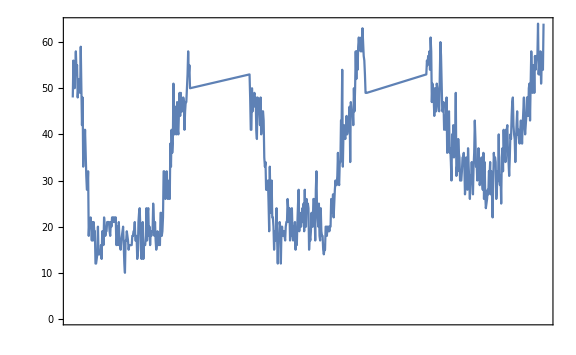

```mathematica
DateListPlot[TimeSeries[Table[EdgeCount[network5m⟦i⟧],{i,1,Length[network5m]}],
{KDS2⟦All,2⟧}],FrameTicks->{{Automatic,Automatic},{{"Thu 12 Oct 2017 07:00:00",
"Thu 12 Oct 2017 11:00:00","Thu 12 Oct 2017 15:00:00","Thu 12 Oct 2017 19:00:00",
"Thu 12 Oct 2017 23:00:00","Fri 13 Oct 2017 07:00:00","Fri 13 Oct 2017 11:00:00",
"Fri 13 Oct 2017 15:00:00","Fri 13 Oct 2017 19:00:00","Fri 13 Oct 2017 23:00:00",
"Sat 14 Oct 2017 07:00:00","Sat 14 Oct 2017 11:00:00","Sat 14 Oct 2017 15:00:00",
"Sat 14 Oct 2017 19:00:00","Sat 14 Oct 2017 23:00:00"},Automatic}},
DateTicksFormat->{"MonthNameShort"," ","Day","\n","Hour24Short",":00"},ImageSize->Large]
```

#### Наложение по дням

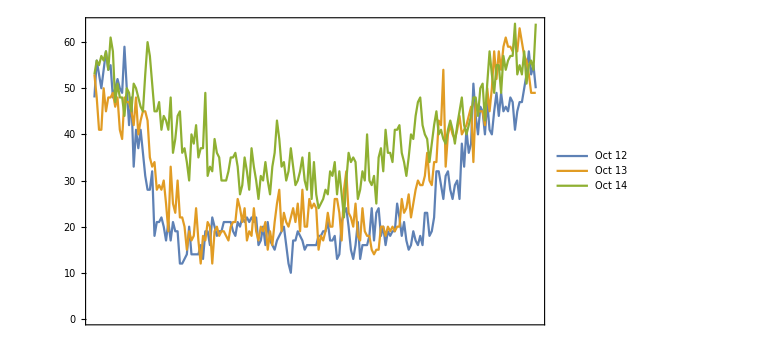

```mathematica
DateListPlot[{TimeSeries[Table[EdgeCount[network5m⟦i⟧],{i,1,192}],
{Flatten[Table[StringCases[KDS2⟦i,2⟧,RegularExpression["..:..:.."]],{i,1,192}]]}],
TimeSeries[Table[EdgeCount[network5m⟦i⟧],{i,193,384}],
{Flatten[Table[StringCases[KDS2⟦i,2⟧,RegularExpression["..:..:.."]],{i,1,192}]]}],
TimeSeries[Table[EdgeCount[network5m⟦i⟧],{i,385,576}],
{Flatten[Table[StringCases[KDS2⟦i,2⟧,RegularExpression["..:..:.."]],{i,1,192}]]}]},
PlotLegends->{"Oct 12","Oct 13","Oct 14"},ImageSize->Large]
```

Зависимость числа ребер от времени суток стала более выраженной (Разница между минимум и максимумом более чем в три раза). Среднее количество ребер в сети:

```mathematica
N[Mean[Table[EdgeCount[network5m⟦i⟧],{i,1,Length[network5m]}]]]
```

32.8663

Средняя плотность:

```mathematica
N[Mean[Table[GraphDensity[network5m⟦i⟧],{i,1,Length[network5m]}]]]
```

0.000299476

Средняя степень вершины:

```mathematica
N[Mean[Table[Mean[VertexDegree[network5m⟦i⟧]],{i,1,Length[network5m]}]]]
```

0.140155

#### Динамика изменения ассортативности сети во времени

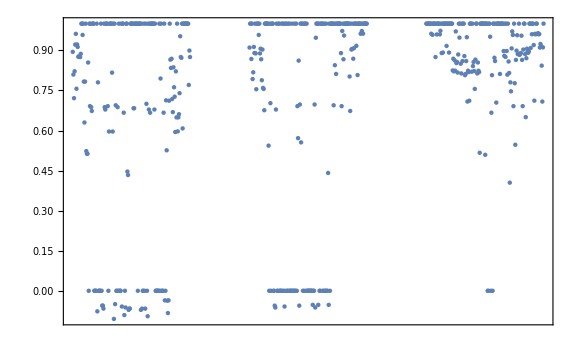

```mathematica
DateListPlot[TimeSeries[Table[GraphAssortativity[network5m⟦i⟧],{i,1,Length[network5m]}],
{KDS2⟦All,2⟧}],FrameTicks->{{Automatic,Automatic},{{"Thu 12 Oct 2017 07:00:00",
"Thu 12 Oct 2017 11:00:00","Thu 12 Oct 2017 15:00:00","Thu 12 Oct 2017 19:00:00",
"Thu 12 Oct 2017 23:00:00","Fri 13 Oct 2017 07:00:00","Fri 13 Oct 2017 11:00:00",
"Fri 13 Oct 2017 15:00:00","Fri 13 Oct 2017 19:00:00","Fri 13 Oct 2017 23:00:00",
"Sat 14 Oct 2017 07:00:00","Sat 14 Oct 2017 11:00:00","Sat 14 Oct 2017 15:00:00",
"Sat 14 Oct 2017 19:00:00","Sat 14 Oct 2017 23:00:00"},Automatic}},
DateTicksFormat->{"MonthNameShort"," ","Day","\n","Hour24Short",":00"},Joined->False,ImageSize->Large]
```

Из за малого количества ребер при большом количестве вершин значение ассортативности теперь чаще либо максимальное (единица), либо нейтральное (ноль), однако среднее значение при этом практически не изменилось:

```mathematica
N[Mean[Table[GraphAssortativity[network5m⟦i⟧],{i,1,Length[network5m]}]]]
```

0.726977

#### Динамика изменения глобального коэффициента кластеризации сети во времени

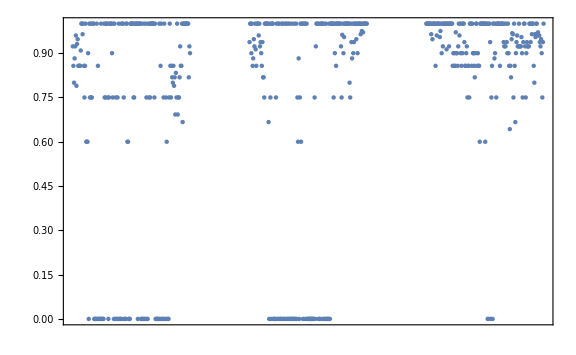

```mathematica
DateListPlot[TimeSeries[Table[GlobalClusteringCoefficient[network5m⟦i⟧],{i,1,Length[network5m]}],
{KDS2⟦All,2⟧}],FrameTicks->{{Automatic,Automatic},{{"Thu 12 Oct 2017 07:00:00",
"Thu 12 Oct 2017 11:00:00","Thu 12 Oct 2017 15:00:00","Thu 12 Oct 2017 19:00:00",
"Thu 12 Oct 2017 23:00:00","Fri 13 Oct 2017 07:00:00","Fri 13 Oct 2017 11:00:00",
"Fri 13 Oct 2017 15:00:00","Fri 13 Oct 2017 19:00:00","Fri 13 Oct 2017 23:00:00",
"Sat 14 Oct 2017 07:00:00","Sat 14 Oct 2017 11:00:00","Sat 14 Oct 2017 15:00:00",
"Sat 14 Oct 2017 19:00:00","Sat 14 Oct 2017 23:00:00"},Automatic}},
DateTicksFormat->{"MonthNameShort"," ","Day","\n","Hour24Short",":00"},Joined->False,ImageSize->Large]
```

Как и ассортативность из за крайне низкой плотности значения коэффициента либо максимальные либо минимальные. Среднее значение практически не изменилось:

```mathematica
N[Mean[Table[GlobalClusteringCoefficient[network5m⟦i⟧],{i,1,Length[network5m]}]]]
```

0.745444

## Увеличение времени обновления состояния в сети

В исследуемой сети время временной интервал обновления состояния составляет 5 минут. Моделирование распространения эпидемии происходит на протяжении как минимум нескольких дней. По этой причине для уменьшения временных затрат при моделировании необходимо увеличить интервал обновления состояния сети. Так же в дальнейшем мы будем сравнивать результаты моделирования на статичной сети и сети изменяемой во времени. Для этого напишем функцию которая будет объединять состояния сети увеличивая тем самым временной интервал обновления. Вес ребра при объединении N временных промежутков будет считаться по свойствам вероятности, т.е. если мы хотим получить вероятность заражения за общий промежуток времени, то мы перемножаем вероятности того что вершина не заразится на каждом интервале и вычитаем из единицы полученное произведение: w_union=1-∏_(i=1)^N (1-w_i). На вход функции подается список ребер, список весов ребер, первая временная отсечка, последняя временная отсечка, количество временных шагов, которое мы объединяем в один шаг. На выходе мы получаем список ребер и список весов ребер.

```mathematica
NetUnion[el_,we_,tstart_,tend_,tstep_]:=
Module[{data=Table[Normal[GroupBy[{Flatten[el⟦i;;i+tstep-1⟧],
Flatten[we⟦i;;i+tstep-1⟧]}ᵀ,First]]⟦All,2⟧,{i,1,tend-tstep+1,tstep}]},
data=Table[{DeleteDuplicates[Flatten[data⟦i,All,All,1⟧]],Table[1-Times@@(1-data⟦i,k,All,2⟧),
{k,1,Length[data⟦i⟧]}]},{i,1,(tend-tstart+1)/tstep}];{data⟦All,1⟧,data⟦All,2⟧}]
```

Рассмотрим сеть с обновлением состояния раз в 1 час, 16 часов (день наблюдений) и единую сеть за три дня.

## Обновление раз в час

```mathematica
up1h=NetUnion[edgelist,w,1,Length[KDS2],12];
up1h5m=NetUnion[edgelist5m,w5m,1,Length[KDS2],12];
td1h=Table[KDS2⟦i,2⟧,{i,1,Length[KDS2],12}];
```

## Обновление раз в день

```mathematica
up1d=NetUnion[edgelist,w,1,Length[KDS2],192];
up1d5m=NetUnion[edgelist5m,w5m,1,Length[KDS2],192];
td1d={"Thu 12 Oct 2017","Fri 13 Oct 2017", "Sat 14 Oct 2017"};
```

## Единая сеть

```mathematica
fn=NetUnion[edgelist,w,1,Length[KDS2],Length[KDS2]];
fn5m=NetUnion[edgelist5m,w5m,1,Length[KDS2],Length[KDS2]];
tdfn={"12-14 Oct 2017"};
```

## Исследование единой сети

Визуализируем полученную сеть расположив вершины в виде квадратной решетки.

#### Визуализация единой сети

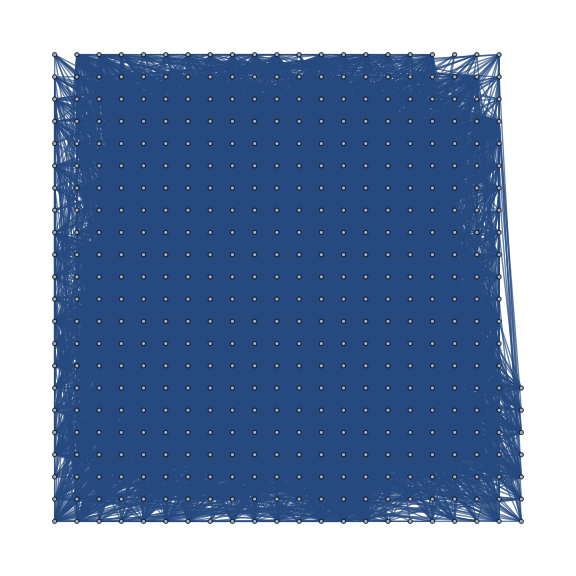

```mathematica
fng=EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],fn⟦1,1⟧,
VertexCoordinates->Table[i->grid⟦i⟧,{i,1,vertexcount}],
EdgeWeight->Table[fn⟦1,1,i⟧->fn⟦2,1,i⟧,{i,1,Length[fn⟦1,1⟧]}],ImageSize->Large]
```

#### Визуализация единой сети в которой отброшены все ребра с расстоянием более 5 метров

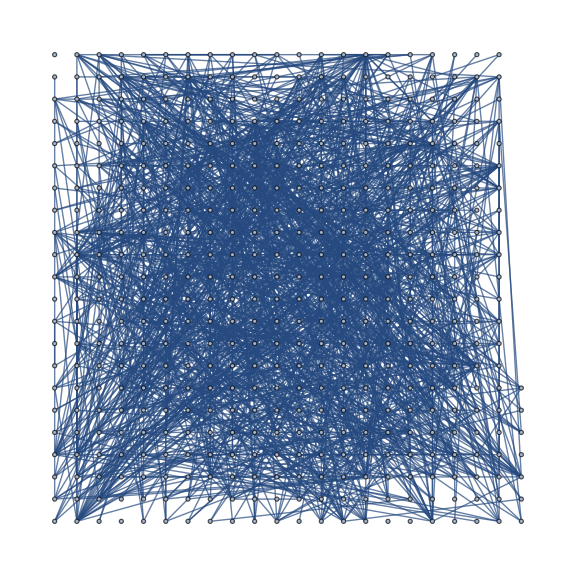

```mathematica
fng5m=EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],fn5m⟦1,1⟧,
VertexCoordinates->Table[i->grid⟦i⟧,{i,1,vertexcount}],
EdgeWeight->Table[fn5m⟦1,1,i⟧->fn5m⟦2,1,i⟧,{i,1,Length[fn5m⟦1,1⟧]}],ImageSize->Large]
```

Рассмотрим характеристики единой сети

#### Характеристики сети

```mathematica
Grid[{{"Характеристика","Значение"},{"Число вершин",VertexCount[fng]},
{"Число ребер",EdgeCount[fng]},{"Плотность",N[GraphDensity[fng]]},
{"Средняя степень вершины",N[Mean[VertexDegree[fng]]]},
{"Коэффициент ассортативности",N[GraphAssortativity[fng]]},
{"Коэффициент глобальной кластеризации",N[GlobalClusteringCoefficient[fng]]}},
Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},
Frame->True,Spacings->{2,{2,{0.7},2}}]
```

Характеристика | Значение
Число вершин | 469
Число ребер | 8277
Плотность | 0.0754196
Средняя степень вершины | 35.2964
Коэффициент ассортативности | 0.129071
Коэффициент глобальной кластеризации | 0.219703

#### Характеристики сети в которой отброшены все ребра с расстоянием более 5 метров

```mathematica
Grid[{{"Характеристика","Значение"},{"Число вершин",VertexCount[fng5m]},
{"Число ребер",EdgeCount[fng5m]},{"Плотность",N[GraphDensity[fng5m]]},
{"Средняя степень вершины",N[Mean[VertexDegree[fng5m]]]},
{"Коэффициент ассортативности",N[GraphAssortativity[fng5m]]},
{"Коэффициент глобальной кластеризации",N[GlobalClusteringCoefficient[fng5m]]}},
Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},
Frame->True,Spacings->{2,{2,{0.7},2}}]
```

Характеристика | Значение
Число вершин | 469
Число ребер | 1350
Плотность | 0.0123011
Средняя степень вершины | 5.75693
Коэффициент ассортативности | 0.12871
Коэффициент глобальной кластеризации | 0.179232

## Моделирование распространения эпидемии. SIR модель

Британские ученые Андерсон Кермак и Уильям Маккендрик разработали широко применяемую сегодня модель SIR. Эта аббревиатура происходит от английских слов Susceptible — Infected — Recovered, буквально означающих «восприимчивые — инфицированные — выздоровевшие». Под «восприимчивыми» тут подразумеваются еще не инфицированные организмы. В рамках этой модели с помощью систем дифференциальных уравнений (при условии непрерывности времени и большой популяции) или разностных уравнений (при дискретном времени и ограниченной популяции) описывается динамика распространения заболевания. SIR–модель получила заслуженную популярность в силу простоты построения и использования. Система уравнений SIR:
Piecewise[{{(∂S)/(∂t)=-(β I S)/N, }, {(∂I)/(∂t)=(β I S)/N-γ I, }, {(∂R)/(∂t)=γ I, }}]
Условие (∂S)/(∂t)+(∂I)/(∂t)+(∂R)/(∂t)=0 описывает неизменность численности популяции (и не учитывает случаи смерти от заболевания).
Где S(t) - численность восприимчивых индивидов в момент времени t;
I(t) - численность инфицированных индивидов в момент времени t;
R(t) - численность переболевших индивидов в момент времени t;
β - коэффициент интенсивности контактов индивидов с последующим инфицированием;
γ - коэффициент интенсивности выздоровления инфицированных индивидов.
Первое уравнение системы означает, что изменение числа здоровых (и при этом восприимчивых к заболеванию) индивидуумов уменьшается со временем пропорционально числу контактов с инфицированными. После контакта происходит заражение, восприимчивый переходит в состояние инфицированного. Второе уравнение показывает, что скорость увеличения числа заразившихся растет пропорционально числу контактов здоровых и инфицированных и уменьшается по мере выздоровления последних. Третье уравнение демонстрирует, что число выздоровевших в единицу времени пропорционально числу инфицированных. Иначе говоря, каждый заболевший через некоторое время должен поправиться. Таким образом, мы видим, что заболевание в модели SIR развивается по схеме «восприимчивые становятся инфицированными, потом выздоравливают». Последнее условие описывает неизменность численности популяции.

#### График перехода состояний в SIR модели

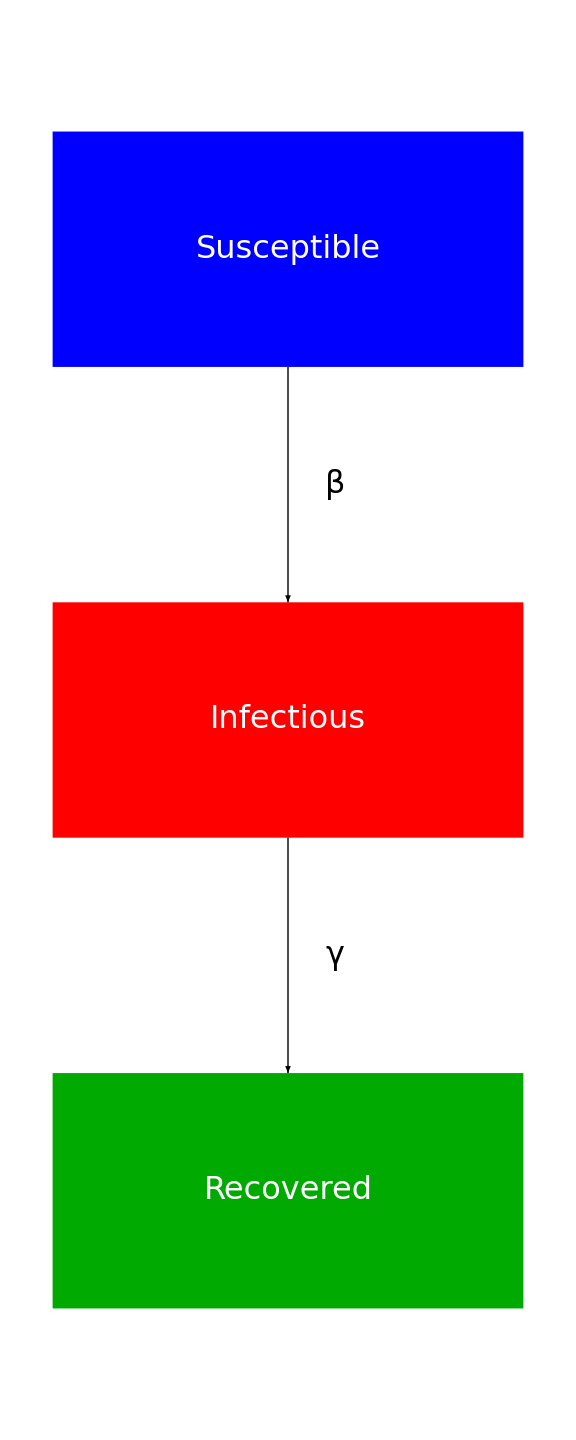

```mathematica
Graphics[{Blue,Rectangle[{2,-1},{4,-2},RoundingRadius->1/3],
White,Text[Style["Susceptible",32],{3,-3/2}],Red,Rectangle[{2,-3},{4,-4},RoundingRadius->1/3],
White,Text[Style["Infectious",32],{3,-7/2}],Darker[Green],Rectangle[{2,-5},{4,-6},RoundingRadius->1/3],
White,Text[Style["Recovered",32],{3,-11/2}],Black,Arrow[{{3,-2},{3,-3}}],Arrow[{{3,-4},{3,-5}}],
Text[Style["β",32],{16/5,-5/2}],Text[Style["γ",32],{16/5,-9/2}]},ImageSize->Large]
```

#### Интерактивный график SIR модели

```mathematica
Manipulate[ListLinePlot[Transpose[NestList[{#⟦1⟧(1-b#⟦2⟧),(1-c)#⟦2⟧+b#⟦2⟧#⟦1⟧,#⟦3⟧+c#⟦2⟧}&,
{1-i0,i0,0},150]],PlotLegends->{"Восприимчивые","Инфицированные","Выздоровевшие"},
PlotStyle->{Blue,Red,Darker[Green]},PlotRange->{{0,150},{0,1}}],
{{b,0.25,"Вероятность заражения"},0,0.9,Appearance->"Labeled"},
{{c,0.1,"Вероятность выздоровления"},0,0.9,Appearance->"Labeled"},
{{i0,0.01,"Доля инфицированных в начале"},0,1,Appearance->"Labeled"}]
```

## SIR модель на графе. Исследование зависимости характеристик вершин от их потенциала к заражению.

Применимо к графам SIR модель работает следующим образом. В конкретный момент времени каждая вершина в графе может быть в одном из трех состояний: восприимчивый (susceptible), зараженный (infected) и выздоровевший (recovered). Перед началом моделирования случайно (или при необходимости конкретно) выбираются одна или несколько вершин и их статус меняется на инфицированных. У остальных вершин восприимчивый статус. Затем на каждом шаге создается список инфицированных на текущий момент времени вершин, и каждая из этих вершин пытается заразить своих восприимчивых соседей (есть ребро между вершинами) с заданной заранее вероятностью. В нашем случае у каждого ребра своя вероятность. После этого для каждой инфицированной вершины с заданной вероятностью статус может поменяться на выздоровевшую. Моделирование продолжается либо до момента, когда все вершины стали выздоровевшие либо до заданной временной отсечки. На первом этапе рассмотрим разницу при моделировании на сети со всеми ребрами и на сети где были отброшены ребра с расстоянием более 5 метров.

Вспомогательная функция которая для каждой вершины графа выдает список соседних вершин и веса ребер между ними.

```mathematica
NearestNeighborList[el_,ew_,vc_]:=
Module[{data=Sort[Partition[Flatten[{{el⟦All,1⟧,el⟦All,2⟧,ew}ᵀ,{el⟦All,2⟧,el⟦All,1⟧,ew}ᵀ}],3]]},
data=Table[{Cases[data,{i,_,_}]⟦All,2⟧,Cases[data,{i,_,_}]⟦All,3⟧},{i,1,vc}];data]
```

SIR модель. На вход подается список ребер и их весов для каждого момента времени, количество вершин, инфицированных в начале, вероятность заражения (при 1 вероятность будет равна весу ребра) и выздоровления. На выходе список с состоянием вершин для каждого момента времени.

```mathematica
SIR[ele_,ewe_,vc_,i0_,β_,μ_]:=
Module[{predata=Table[NearestNeighborList[ele⟦i⟧,ewe⟦i⟧,vc],{i,1,Length[ele]}],
data=Table[{i,"Susceptible",{},{}},{j,1,Length[ele]},{i,1,vc}],iv={},rv={}},
Do[Do[data⟦i,j,3⟧=predata⟦i,j,1⟧;data⟦i,j,4⟧=predata⟦i,j,2⟧,{j,1,vc}],{i,1,Length[ele]}];
iv=RandomSample[Range[vc],i0];Do[data⟦1,iv⟦i⟧,2⟧="Infected",{i,1,i0}];
Do[rv=Cases[data⟦i⟧,{_,"Recovered",_,_}];
If[rv≠{},Do[data⟦i+1,rv⟦j,1⟧,2⟧="Recovered",{j,1,Length[rv]}]];
iv=Cases[data⟦i⟧,{_,"Infected",_,_}];
If[iv≠{},Do[data⟦i+1,iv⟦j,1⟧,2⟧="Infected",{j,1,Length[iv]}];
Do[If[iv⟦j,3⟧≠{},Do[If[RandomChoice[{β iv⟦j,4,k⟧,1-β iv⟦j,4,k⟧}->{True,False}]==True,
If[data⟦i,iv⟦j,3,k⟧,2⟧=="Susceptible",data⟦i+1,iv⟦j,3,k⟧,2⟧="Infected"]],
{k,1,Length[iv⟦j,3⟧]}]],{j,1,Length[iv]}];
Do[If[RandomChoice[{μ,1-μ}->{True,False}]==True,data⟦i+1,iv⟦j,1⟧,2⟧="Recovered"],
{j,1,Length[iv]}]],{i,1,Length[ele]-1}];data]
```

Вспомогательная функция для дублирования массива.

```mathematica
DA[ar_,n_]:=Table[ar⟦Mod[i,Length[ar]]+1⟧,{i,0,n-1}]
```

Вспомогательная функция для моделирования.

```mathematica
SIRmod[ele_,ewe_,vc_,i0_,β_,μ_,n_]:=
Mean[Table[Module[{out=SIR[ele,ewe,vc,i0,β,μ]},Table[{Length[Cases[out⟦i⟧,{_,"Susceptible",_,_}]],
Length[Cases[out⟦i⟧,{_,"Infected",_,_}]],Length[Cases[out⟦i⟧,{_,"Recovered",_,_}]]},
{i,1,Length[out]}]],{l,1,n}]]
```

Вспомогательная функция для построения графиков.

```mathematica
SIRplot[data_,dt1_,dt2_]:=ListLinePlot[Table[{j,data⟦j,i⟧},{i,1,3},{j,1,Length[data]}],
PlotRange->{{0,Length[data]},{0,Total[data⟦1⟧]}},
Ticks->{Table[{dt1 i,i},{i,0,Round[Length[data]/dt1],dt2}],Automatic},
PlotLegends->Placed[{"Восприимчивые","Инфицированные","Выздоровевшие"},Bottom],
PlotStyle->{Blue,Red,Darker[Green]},ImageSize->Large]
```

Предположим что вероятность выздоровления за один день составляет 0.1. Тогда вероятность за один час (при условии, что за день наблюдений собираются данные за 16 часов) составляет:

```mathematica
γ1h=Solve[1-(1-pγ)^16==0.1&&0<pγ<1,pγ]⟦1,1,2⟧
```

0.0065634

Моделирование на сети со всеми ребрами. Обновление состояния сети раз в час. Усреднение по 100 запускам.

```mathematica
sir1hn=Import[FileNameJoin[{NotebookDirectory[],"sir1hn.m"}]];
(*sir1hn=SIRmod[DA[up1h⟦1⟧,50 16],DA[up1h⟦2⟧,50 16],vertexcount,5,1,γ1h,100];*)
```

#### График

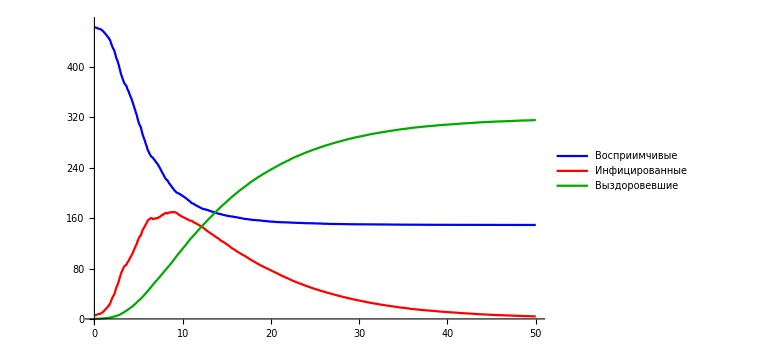

```mathematica
SIRplot[sir1hn,16,10]
```

Моделирование на сети где отброшены ребра с расстоянием более 5 метров.

```mathematica
sir1hn5m=Import[FileNameJoin[{NotebookDirectory[],"sir1hn5m.m"}]];
(*sir1hn=SIRmod[DA[up1h5m⟦1⟧,50 16],DA[up1h5m⟦2⟧,50 16],vertexcount,5,1,γ1h,100];*)
```

#### График

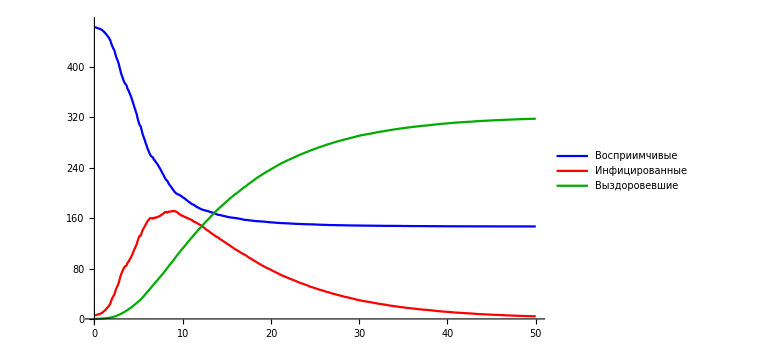

```mathematica
SIRplot[sir1hn5m,16,10]
```

#### Наложение графиков

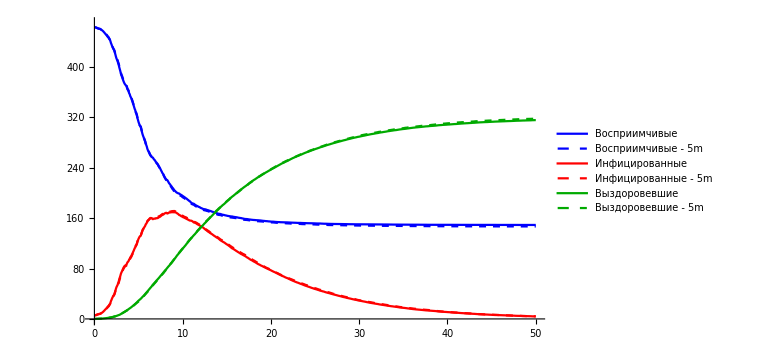

```mathematica
ListLinePlot[{Table[{i,sir1hn⟦i,1⟧},{i,1,Length[sir1hn]}],
Table[{i,sir1hn5m⟦i,1⟧},{i,1,Length[sir1hn5m]}],Table[{i,sir1hn⟦i,2⟧},{i,1,Length[sir1hn]}],
Table[{i,sir1hn5m⟦i,2⟧},{i,1,Length[sir1hn5m]}],Table[{i,sir1hn⟦i,3⟧},{i,1,Length[sir1hn]}],
Table[{i,sir1hn5m⟦i,3⟧},{i,1,Length[sir1hn5m]}]},PlotRange->{{0,800},{0,vertexcount}},
Ticks->{Table[{16i,i},{i,0,50,10}],Automatic},PlotLegends->Placed[{"Восприимчивые",
"Восприимчивые - 5m","Инфицированные","Инфицированные - 5m",
"Выздоровевшие","Выздоровевшие - 5m"},Bottom],
PlotStyle->{Blue,{Blue,Dashed},Red,{Red,Dashed},Darker[Green],{Darker[Green],Dashed}},
ImageSize->Large]
```

Расхождение между двумя графиками минимальное. По этой причине для уменьшения затрат времени на дальнейшее моделирование мы будем пользоваться сетью в которой отброшены ребра с расстоянием более 5 метров. Рассмотрим зависимость характеристик вершин от их потенциала к заражению. Для этого упростим нашу модель до SI (мы будем рассматривать первые 10 дней заражения, поэтому можно пренебречь R составляющей) и добавим возможность задать конкретную вершину с которой пойдет распространение эпидемии. Так же изменим выход функции. Нас интересует только итоговая сумма зараженных.

```mathematica
SI[ele_,ewe_,vc_,i0_]:=
Module[{predata=Table[NearestNeighborList[ele⟦i⟧,ewe⟦i⟧,vc],{i,1,Length[ele]}],
data=Table[{i,"Susceptible",{},{}},{j,1,Length[ele]},{i,1,vc}],iv={},out={}},
Do[Do[data⟦i,j,3⟧=predata⟦i,j,1⟧;data⟦i,j,4⟧=predata⟦i,j,2⟧,{j,1,vc}],{i,1,Length[ele]}];
data⟦1,i0,2⟧="Infected";Do[iv=Cases[data⟦i⟧,{_,"Infected",_,_}];
If[iv≠{},Do[data⟦i+1,iv⟦j,1⟧,2⟧="Infected",{j,1,Length[iv]}];
Do[If[iv⟦j,3⟧≠{},Do[If[RandomChoice[{ iv⟦j,4,k⟧,1- iv⟦j,4,k⟧}->{True,False}]==True,
If[data⟦i,iv⟦j,3,k⟧,2⟧=="Susceptible",data⟦i+1,iv⟦j,3,k⟧,2⟧="Infected"]],
{k,1,Length[iv⟦j,3⟧]}]],{j,1,Length[iv]}]],{i,1,Length[ele]-1}];
out=Length[Cases[data⟦-1⟧,{_,"Infected",_,_}]];out]
```

Для каждой вершины в сети мы моделируем по 10 раз распространение эпидемии стартующее с этой вершины. Усредняем полученные данные и ранжируем итоговый список. Таким образом мы получили список вершин давших наибольший уровень заражения в целом по сети.

```mathematica
rank=Import[FileNameJoin[{NotebookDirectory[],"rank.m"}]];
(*rank=ReverseSortBy[Table[{m,N[Mean[Table[SI[DA[up1h5m⟦1⟧,10 16],
DA[up1h5m⟦2⟧,10 16],vertexcount,m],{l,1,10}]]]},{m,1,vertexcount}],Last];*)
```

Средние характеристики вершин.

```mathematica
vc=Mean[Table[Module[{in=EdgeAdd[AdjacencyGraph[Table[0,{i,1,vertexcount},{j,1,vertexcount}]],
up1h5m⟦1,l⟧]},SortBy[{VertexList[in],DegreeCentrality[in],ClosenessCentrality[in],
BetweennessCentrality[in],EigenvectorCentrality[in],LocalClusteringCoefficient[in]}ᵀ,First]],
{l,1,Length[up1h5m⟦1⟧]}]];
```

#### Топ 10 вершин по потенциалу заражения

```mathematica
Grid[Partition[Flatten[{"Номер вершины","Среднее количество зараженных в сети через 10 дней",
"Средняя центральность по степени","Средняя центральность по близости",
Table[{rank⟦i⟧,N[vc⟦rank⟦i,1⟧⟧⟦2;;3⟧]},{i,1,10}],"Номер вершины",
"Средняя центральность по посредничеству","Средняя степень влиятельности",
"Средний локальный коэффициент кластеризации",
Table[{rank⟦i,1⟧,N[vc⟦rank⟦i,1⟧⟧⟦4;;6⟧]},{i,1,10}]}],4],
Background->{None,{1->GrayLevel[0.7],12->GrayLevel[0.7]}},Dividers->{Black,
{2->Black,12->Black,13->Black}},Frame->True,Spacings->{2,2}]
```

Номер вершины | Среднее количество зараженных в сети через 10 дней | Средняя центральность по степени | Средняя центральность по близости
342 | 321.6 | 0.979167 | 0.622964
215 | 320.3 | 1.35417 | 0.432326
73 | 318.1 | 1.0625 | 0.639389
330 | 317.6 | 2.54167 | 0.483086
12 | 317.4 | 0.75 | 0.606859
14 | 317. | 0.9375 | 0.403745
375 | 316.5 | 1.25 | 0.32204
311 | 315.7 | 1.6875 | 0.5932
301 | 315.6 | 1.20833 | 0.44424
228 | 315.6 | 1.0625 | 0.263657
Номер вершины | Средняя центральность по посредничеству | Средняя степень влиятельности | Средний локальный коэффициент кластеризации
342 | 1.03125 | 0.00620936 | 0.04375
215 | 6.58333 | 0.00619406 | 0.125
73 | 0.631944 | 0.00631722 | 0.121032
330 | 14.2222 | 0.0116966 | 0.269246
12 | 0.5625 | 0.00455398 | 0.0208333
14 | 4.8125 | 0.00627165 | 0.0916667
375 | 8.27431 | 0.0055104 | 0.0861111
311 | 6.9375 | 0.00902232 | 0.131944
301 | 0.0121528 | 0.0055912 | 0.4375
228 | 0.770833 | 0.00442005 | 0.409722

Составим теперь списки вершин отсортированных по различным характеристикам. Средняя центральность по степени:

```mathematica
tdc=ReverseSortBy[{vc⟦All,1⟧,vc⟦All,2⟧}ᵀ,Last]⟦1;;20⟧;
```

Средняя центральность по близости:

```mathematica
tcc=ReverseSortBy[{vc⟦All,1⟧,vc⟦All,3⟧}ᵀ,Last]⟦1;;20⟧;
```

Средняя центральность по посредничеству:

```mathematica
tbc=ReverseSortBy[{vc⟦All,1⟧,vc⟦All,4⟧}ᵀ,Last]⟦1;;20⟧;
```

Средняя центральность влиятельности:

```mathematica
tec=ReverseSortBy[{vc⟦All,1⟧,vc⟦All,5⟧}ᵀ,Last]⟦1;;20⟧;
```

Средний локальный коэффициент кластеризации:

```mathematica
tlcc=ReverseSortBy[{vc⟦All,1⟧,vc⟦All,6⟧}ᵀ,Last]⟦1;;20⟧;
```

Составим таблицу в которой будет показано сколько вершин из топ 20 по какой-либо характеристике также находятся в топ 20 по уровню заражения.

#### Зависимость потенциала вершины к заражению от ее характеристик

```mathematica
Grid[{{"Характеристика",
"Количество вершин из топ 20 по характеристике которые входят в топ 20 по уровню заражения"},
{"Средняя центральность по степени",Length[rank⟦1;;20,1⟧∩tdc⟦All,1⟧]},
{"Средняя центральность по близости",Length[rank⟦1;;20,1⟧∩tcc⟦All,1⟧]},
{"Средняя центральность по посредничеству",Length[rank⟦1;;20,1⟧∩tbc⟦All,1⟧]},
{"Средняя центральность влиятельности",Length[rank⟦1;;20,1⟧∩tec⟦All,1⟧]},
{"Средний локальный коэффициент кластеризации",Length[rank⟦1;;20,1⟧∩tlcc⟦All,1⟧]}},
Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},
Frame->True,Spacings->{2,{2,{0.7},2}}]
```

Характеристика | Количество вершин из топ 20 по характеристике которые входят в топ 20 по уровню заражения
Средняя центральность по степени | 6
Средняя центральность по близости | 0
Средняя центральность по посредничеству | 9
Средняя центральность влиятельности | 5
Средний локальный коэффициент кластеризации | 5

<ТЕКСТ ПРО ВЫВОДЫ>

## SEIRD модель

По SIER модели развиваются по-настоящему опасные эпидемии, поскольку длительный инкубационный период может препятствовать своевременному обнаружению заболевания. В этом случае есть риск, что заболевание охватит значительное число индивидуумов в популяции.
Инфекция развивается по схеме «восприимчивые» — «контактные» — «инфицированные» — «выздоровевшие» и описывается системой уравнений:
Piecewise[{{(∂S)/(∂t)=μ N-μ S-β I/N S, }, {(∂E)/(∂t)=β I/N S-(μ+α)E, }, {(∂I)/(∂t)=α E-(γ+μ)I, }, {(∂R)/(∂t)=γ I-μ R, }}]
Где μ - уровень смертности;
α - величина, обратная среднему инкубационному периоду заболевания;
E(t) - численность индивидов — носителей заболевания в момент времени t.
Как и в модели SIR, первое уравнение системы означает, что изменение числа здоровых (и при этом восприимчивых к заболеванию) индивидуумов уменьшается со временем пропорционально числу контактов с инфицированными. После заражения здоровый индивид переходит в состояние контактного по данному заболеванию, или носителя инфекции.
Второе уравнение вносит задержку по времени при переходе из состояния контактного в состояние инфицированного (больного). Это происходит через время, равное инкубационному периоду болезни.
Третье уравнение описывает переход из состояния «контактный» в состояние «инфицированный».
Четвертое уравнение демонстрирует, что число выздоровевших в единицу времени пропорционально числу инфицированных. При этом в каждом состоянии индивидуум может погибнуть, что учитывает коэффициент μ в каждом уравнении.
Иначе говоря, в каждый момент времени каждый индивидуум с определенной вероятностью может заразиться, через некоторое время — заболеть, а затем поправиться либо погибнуть.
Численность популяции N=S+E+I+R при том не является постоянной с течением времени, однако возможно модифицировать модель, добавив в неё пятое состояние - умершие (Dead). В такой ситуации N=S+E+I+R+D=Const.
Система уравнений в SEIRD модели принимает такой вид:
Piecewise[{{(∂S)/(∂t)=-β/NS I, }, {(∂E)/(∂t)=β/N S I-ϵ E, }, {(∂I)/(∂t)=ϵ E-γ I-α I, }, {(∂R)/(∂t)=γ I, }, {(∂D)/(∂t)=α I, }}]
Где β - коэффициент перехода из состояния S в E (вероятность заражения);
ϵ - коэффициент перехода из состояния E в I (величина, обратная среднему инкубационному периоду заболевания);
γ - коэффициент перехода из состояния I в R (носитель становится заразным);
α - коэффициент перехода из состояния I в D (уровень смертности).

#### График перехода состояний в SEIRD модели

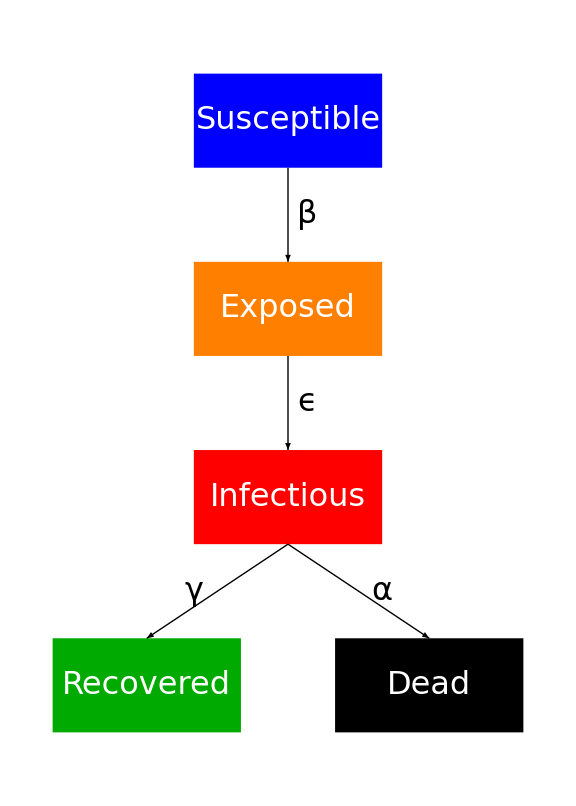

```mathematica
Graphics[{Blue,Rectangle[{2,-1},{4,-2},RoundingRadius->1/3],
White,Text[Style["Susceptible",32],{3,-3/2}],Orange,Rectangle[{2,-3},{4,-4},RoundingRadius->1/3],
White,Text[Style["Exposed",32],{3,-7/2}],Red,Rectangle[{2,-5},{4,-6},RoundingRadius->1/3],
White,Text[Style["Infectious",32],{3,-11/2}],Darker[Green],
Rectangle[{1/2,-7},{5/2,-8},RoundingRadius->1/3],White,Text[Style["Recovered",32],{3/2,-15/2}],
Black,Rectangle[{7/2,-7},{11/2,-8},RoundingRadius->1/3],White,Text[Style["Dead",32],{9/2,-15/2}],
Black,Arrow[{{3,-2},{3,-3}}],Arrow[{{3,-4},{3,-5}}],Arrow[{{3,-6},{3/2,-7}}],
Arrow[{{3,-6},{9/2,-7}}],Text[Style["β",32],{16/5,-5/2}],Text[Style["ϵ",32],{16/5,-9/2}],
Text[Style["γ",32],{2,-13/2}],Text[Style["α",32],{4,-13/2}]},ImageSize->Large]
```

#### Интерактивный график SEIRD модели

```mathematica
Manipulate[ListLinePlot[Transpose[NestList[{#⟦1⟧(1-β#⟦3⟧),#⟦2⟧(1-1/ϵ)+β#⟦1⟧#⟦3⟧,#⟦3⟧(1-γ-α)+1/ϵ#⟦2⟧,
#⟦4⟧+γ#⟦3⟧,#⟦5⟧+α#⟦3⟧}&,{1-i0,0,i0,0,0},150]],PlotLegends->{"Восприимчивые","Контактные",
"Инфицированные","Выздоровевшие","Умершие"},PlotStyle->{Blue,Orange,Red,Darker[Green],Black},
PlotRange->{{0,150},{0,1}}],{{β,0.3,"Вероятность заражения"},0,1,Appearance->"Labeled"},
{{ϵ,7,"Инкубационный период в днях"},0,14,Appearance->"Labeled"},
{{γ,0.1,"Вероятность выздоровления"},0,1,Appearance->"Labeled"},
{{α,0.03,"Вероятность смерти"},0,0.9,Appearance->"Labeled"},
{{i0,0.01,"Доля инфицированных в начале"},0,1,Appearance->"Labeled"}]
```

## SEIRD модель на графе

По сравнению с SIR моделью, в SEIRD модели добавляются два дополнительных состояния: контактные (Exposed) и умершие (Dead). Когда на очередном шаге моделирования срабатывает заражение вершины от инфицированной, то в она переход в статус контактной. На следующих шагах для каждой контактной вершины проходит проверка на превращение в инфицированную вершину с вероятностью равной обратному инкубационному периоду. Пока вершина находится в статусе контактной, она не заражает соседние вершины. Когда у вершины в инфицированном состоянии срабатывает проверка на превращение в состояние выздоровление, то однократно идет проверка на превращение в умершее состояние с вероятностью α.

SEIRD модель. На вход подается список ребер и их весов для каждого момента времени, количество вершин, инфицированных в начале, вероятность перехода в контактное состояние (при 1 вероятность будет равна весу ребра), вероятность перехода в инфицированное состояние (равна обратному инкубационному периоду), вероятность выздоровления и вероятность смерти. На выходе список с состоянием вершин для каждого момента времени.

```mathematica
SEIRD[ele_,ewe_,vc_,i0_,β_,ϵ_,γ_,α_]:=
Module[{predata=Table[NearestNeighborList[ele⟦i⟧,ewe⟦i⟧,vc],{i,1,Length[ele]}],
data=Table[{i,"Susceptible",{},{}},{j,1,Length[ele]},{i,1,vc}],ev={},iv={},rv={},dv={}},
Do[Do[data⟦i,j,3⟧=predata⟦i,j,1⟧;data⟦i,j,4⟧=predata⟦i,j,2⟧,{j,1,vc}],{i,1,Length[ele]}];
iv=RandomSample[Range[vc],i0];Do[data⟦1,iv⟦i⟧,2⟧="Infected",{i,1,i0}];
Do[rv=Cases[data⟦i⟧,{_,"Recovered",_,_}];
If[rv≠{},Do[data⟦i+1,rv⟦j,1⟧,2⟧="Recovered",{j,1,Length[rv]}]];
dv=Cases[data⟦i⟧,{_,"Dead",_,_}];If[dv≠{},Do[data⟦i+1,dv⟦j,1⟧,2⟧="Dead",{j,1,Length[dv]}]];
ev=Cases[data⟦i⟧,{_,"Exposed",_,_}];iv=Cases[data⟦i⟧,{_,"Infected",_,_}];
If[ev≠{},Do[If[RandomChoice[{ϵ,1-ϵ}->{True,False}]==True,data⟦i+1,ev⟦j,1⟧,2⟧="Infected",
data⟦i+1,ev⟦j,1⟧,2⟧="Exposed"],{j,1,Length[ev]}]];If[iv≠{},Do[If[iv⟦j,3⟧≠{},
Do[If[RandomChoice[{β iv⟦j,4,k⟧,1-β iv⟦j,4,k⟧}->{True,False}]==True,
If[data⟦i,iv⟦j,3,k⟧,2⟧=="Susceptible",data⟦i+1,iv⟦j,3,k⟧,2⟧="Exposed"]],{k,1,Length[iv⟦j,3⟧]}]];
If[RandomChoice[{γ,1-γ}->{True,False}]==True,If[RandomChoice[{α,1-α}->{True,False}]==True,
data⟦i+1,iv⟦j,1⟧,2⟧="Dead",data⟦i+1,iv⟦j,1⟧,2⟧="Recovered"],
data⟦i+1,iv⟦j,1⟧,2⟧="Infected"],{j,1,Length[iv]}]],{i,1,Length[ele]-1}];data]
```

Вспомогательная функция для моделирования.

```mathematica
SEIRDmod[ele_,ewe_,vc_,i0_,β_,ϵ_,γ_,α_,n_]:=
Mean[Table[Module[{out=SEIRD[ele,ewe,vc,i0,β,ϵ,γ,α]},
Table[{Length[Cases[out⟦i⟧,{_,"Susceptible",_,_}]],
Length[Cases[out⟦i⟧,{_,"Exposed",_,_}]],Length[Cases[out⟦i⟧,{_,"Infected",_,_}]],
Length[Cases[out⟦i⟧,{_,"Recovered",_,_}]],Length[Cases[out⟦i⟧,{_,"Dead",_,_}]]},
{i,1,Length[out]}]],{l,1,n}]]
```

Вспомогательная функция для построения графиков.

```mathematica
SEIRDplot[data_,dt1_,dt2_]:=ListLinePlot[Table[{j,data⟦j,i⟧},{i,1,5},{j,1,Length[data]}],
PlotRange->{{0,Length[data]},{0,Total[data⟦1⟧]}},
Ticks->{Table[{dt1 i,i},{i,0,Round[Length[data]/dt1],dt2}],Automatic},
PlotLegends->Placed[{"Восприимчивые","Контактные","Инфицированные","Выздоровевшие","Умершие"},Bottom],
PlotStyle->{Blue,Orange,Red,Darker[Green],Black},ImageSize->Large]
```

Вспомогательная функция для построения графиков .

```mathematica
SEIRDplotsum[o1_,o2_,o3_,o4_,o5_,dt1_,dt2_]:=
ListLinePlot[Module[{n=Length[o1]},{Table[{i,o1⟦i,1⟧},{i,1,n}],Table[{i,o2⟦i,1⟧},{i,1,n}],
Table[{i,o3⟦i,1⟧},{i,1,n}],Table[{i,o4⟦i,1⟧},{i,1,n}],Table[{i,o5⟦i,1⟧},{i,1,n}],
Table[{i,o1⟦i,2⟧},{i,1,n}],Table[{i,o2⟦i,2⟧},{i,1,n}],Table[{i,o3⟦i,2⟧},{i,1,n}],
Table[{i,o4⟦i,2⟧},{i,1,n}],Table[{i,o5⟦i,2⟧},{i,1,n}],Table[{i,o1⟦i,3⟧},{i,1,n}],
Table[{i,o2⟦i,3⟧},{i,1,n}],Table[{i,o3⟦i,3⟧},{i,1,n}],Table[{i,o4⟦i,3⟧},{i,1,n}],
Table[{i,o5⟦i,3⟧},{i,1,n}],Table[{i,o1⟦i,4⟧},{i,1,n}],Table[{i,o2⟦i,4⟧},{i,1,n}],
Table[{i,o3⟦i,4⟧},{i,1,n}],Table[{i,o4⟦i,4⟧},{i,1,n}],Table[{i,o5⟦i,4⟧},{i,1,n}],
Table[{i,o1⟦i,5⟧},{i,1,n}],Table[{i,o2⟦i,5⟧},{i,1,n}],Table[{i,o3⟦i,5⟧},{i,1,n}],
Table[{i,o4⟦i,5⟧},{i,1,n}],Table[{i,o5⟦i,5⟧},{i,1,n}]}],
PlotRange->{{0,Length[o1]},{0,Total[o1⟦1⟧]}},
Ticks->{Table[{dt1 i,i},{i,0,Round[Length[o1]/dt1],dt2}],Automatic},
PlotStyle->{{Blue,Dotted},{Blue,Dotted,Thick},{Blue,Dashed},{Blue,Dashed,Thick},{Blue,Thick},
{Orange,Dotted},{Orange,Dotted,Thick},{Orange,Dashed},{Orange,Dashed,Thick},{Orange,Thick},
{Red,Dotted},{Red,Dotted,Thick},{Red,Dashed},{Red,Dashed,Thick},{Red,Thick},
{Darker[Green],Dotted},{Darker[Green],Dotted,Thick},{Darker[Green],Dashed},
{Darker[Green],Dashed,Thick},{Darker[Green],Thick},
{Black,Dotted},{Black,Dotted,Thick},{Black,Dashed},{Black,Dashed,Thick},{Black,Thick}},
PlotLegends->Placed[LineLegend[{"Восприимчивые, время ввода меры - с первого дня",
"Восприимчивые, время ввода меры - через неделю от начала",
"Восприимчивые, время ввода меры - через две недели от начала",
"Восприимчивые, время ввода меры - через три недели от начала",
"Восприимчивые, без ввода мер","Контактные, время ввода меры - с первого дня",
"Контактные, время ввода меры - через неделю от начала",
"Контактные, время ввода меры - через две недели от начала",
"Контактные, время ввода меры - через три недели от начала",
"Контактные, без ввода мер","Инфицированные, время ввода меры - с первого дня",
"Инфицированные, время ввода меры - через неделю от начала",
"Инфицированные, время ввода меры - через две недели от начала",
"Инфицированные, время ввода меры - через три недели от начала",
"Инфицированные, без ввода мер","Выздоровевшие, время ввода меры - с первого дня",
"Выздоровевшие, время ввода меры - через неделю от начала",
"Выздоровевшие, время ввода меры - через две недели от начала",
"Выздоровевшие, время ввода меры - через три недели от начала",
"Выздоровевшие, без ввода мер","Умершие, время ввода меры - с первого дня",
"Умершие, время ввода меры - через неделю от начала",
"Умершие, время ввода меры - через две недели от начала",
"Умершие, время ввода меры - через три недели от начала",
"Умершие, без ввода мер"},LegendLayout->{"Column", 1}],Bottom],ImageSize->Large]
```

Возьмем среднее время инкубационного периода в 7 дней. Тогда за один час получаем:

```mathematica
ϵ1h=N[1/(7 16)]
```

0.00892857

Вероятность заражения и выздоровления оставим такой же как и при SIR моделировании. Вероятность смерти возьмем за 3%.

```mathematica
seird1hn5m=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5m.m"}]];
(*seird1hn5m=SEIRDmod[DA[up1h5m⟦1⟧,16 100],DA[up1h5m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

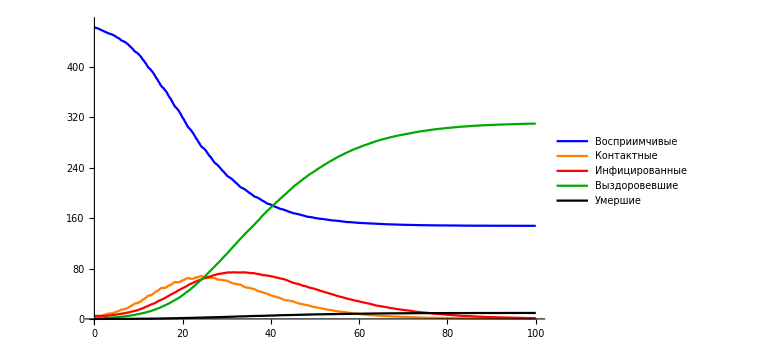

```mathematica
SEIRDplot[seird1hn5m,16,10]
```

## Исследование влияния ограничительных мер на распространение эпидемии. Социальная дистанция

Рассмотрим теперь различные меры по борьбе с эпидемией. Начнем с социальной дистанции. <ТЕКСТ>. Чаще всего рассматривается социальная дистанция в 1 или 2 метра. Создадим копии нашей сети, где расстояния ребер изменены так, что среди них ребер с дистанцией менее чем социальная дистанция.
Социальная дистанция в 1 метр:

```mathematica
up1h5msd1m=NetUnion[edgelist5m,Module[{out=edgelength5m},Do[Do[If[out⟦i,j⟧<1.,out⟦i,j⟧=1.],
{j,1,Length[out⟦i⟧]}],{i,1,Length[out]}];p ⅇ^-out],1,Length[KDS2],12];
```

Социальная дистанция в 2 метра:

```mathematica
up1h5msd2m=NetUnion[edgelist5m,Module[{out=edgelength5m},Do[Do[If[out⟦i,j⟧<2.,out⟦i,j⟧=2.],
{j,1,Length[out⟦i⟧]}],{i,1,Length[out]}];p ⅇ^-out],1,Length[KDS2],12];
```

Произведем моделирование при условиях, что социальная дистанция была введена в первый день эпидемии, через неделю, через две недели, через три недели. Нам потребуется специальная функция, которая будет сначала брать веса в сети до ввода мер, а затем веса после ввода мер.

```mathematica
DA2[ar1_,ar2_,n1_,n2_]:=
Table[If[i<n1,ar1⟦Mod[i,Length[ar1]]+1⟧,ar2⟦Mod[i,Length[ar2]]+1⟧],{i,0,n1+n2-1}]
```

Социальная дистанция - 1 метр, время ввода меры - с первого дня.

```mathematica
seird1hn5msd1m=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5msd1m.m"}]];
(*seird1hn5msd1m=SEIRDmod[DA[up1h5msd1m⟦1⟧,16 100],
DA[up1h5msd1m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

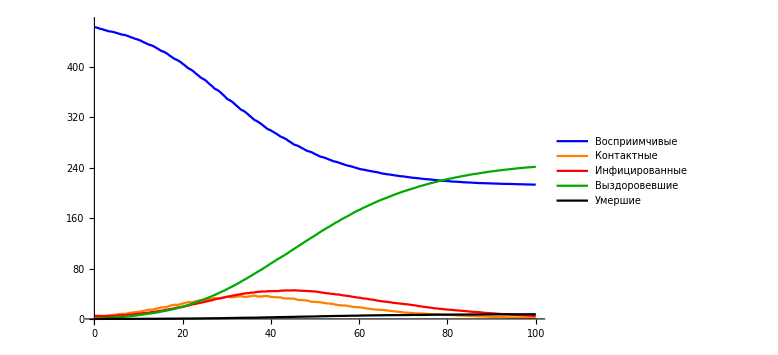

```mathematica
SEIRDplot[seird1hn5msd1m,16,10]
```

Социальная дистанция - 1 метр, время ввода меры - через неделю от начала.

```mathematica
seird1hn5msd1m7d=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5msd1m7d.m"}]];
(*seird1hn5msd1m7d=SEIRDmod[DA2[up1h5m⟦1⟧,up1h5msd1m⟦1⟧,16 7,16 93],
DA2[up1h5m⟦2⟧,up1h5msd1m⟦2⟧,16 7,16 93],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

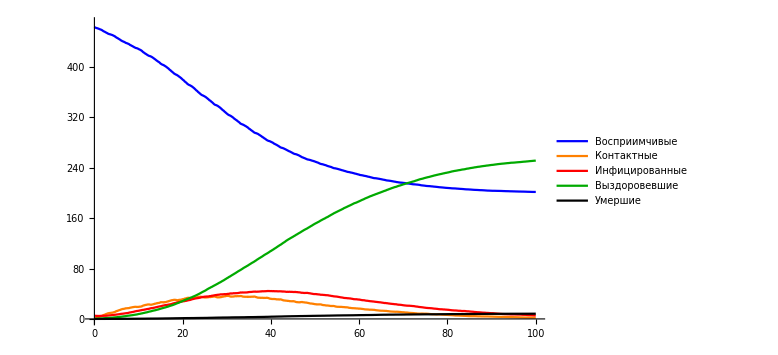

```mathematica
SEIRDplot[seird1hn5msd1m7d,16,10]
```

Социальная дистанция - 1 метр, время ввода меры - через две недели от начала.

```mathematica
seird1hn5msd1m14d=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5msd1m14d.m"}]];
(*seird1hn5msd1m14d=SEIRDmod[DA2[up1h5m⟦1⟧,up1h5msd1m⟦1⟧,16 14,16 86],
DA2[up1h5m⟦2⟧,up1h5msd1m⟦2⟧,16 14,16 86],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

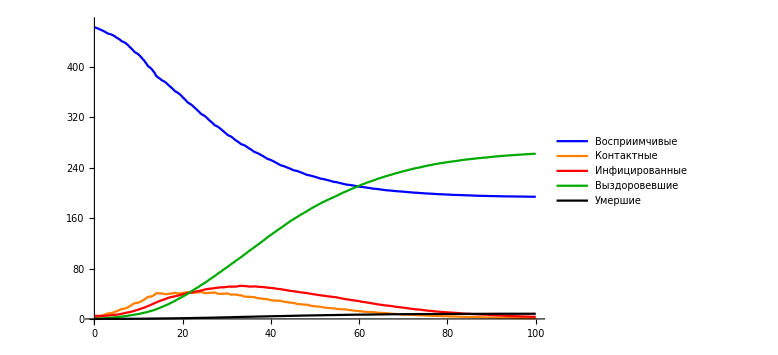

```mathematica
SEIRDplot[seird1hn5msd1m14d,16,10]
```

Социальная дистанция - 1 метр, время ввода меры - через три недели от начала.

```mathematica
seird1hn5msd1m21d=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5msd1m21d.m"}]];
(*seird1hn5msd1m21d=SEIRDmod[DA2[up1h5m⟦1⟧,up1h5msd1m⟦1⟧,16 21,16 79],
DA2[up1h5m⟦2⟧,up1h5msd1m⟦2⟧,16 21,16 79],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

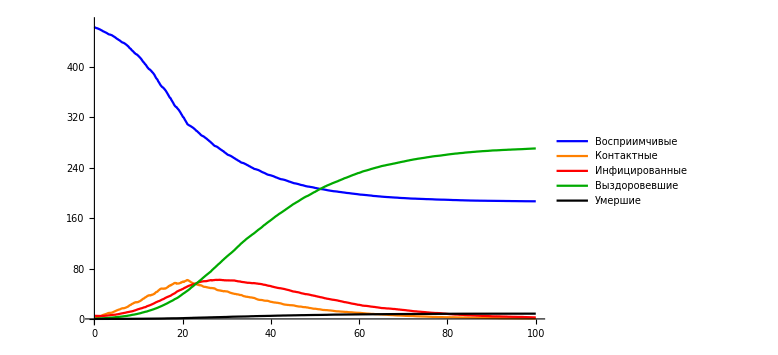

```mathematica
SEIRDplot[seird1hn5msd1m21d,16,10]
```

#### Наложение графиков

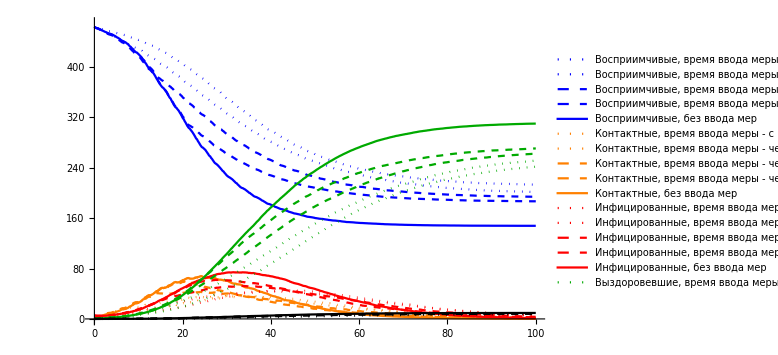

```mathematica
SEIRDplotsum[seird1hn5msd1m,seird1hn5msd1m7d,seird1hn5msd1m14d,seird1hn5msd1m21d,seird1hn5m,16,10]
```

Социальная дистанция - 2 метра, время ввода меры - с первого дня.

```mathematica
seird1hn5msd2m=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5msd2m.m"}]];
(*seird1hn5msd2m=SEIRDmod[DA[up1h5msd2m⟦1⟧,16 100],
DA[up1h5msd2m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

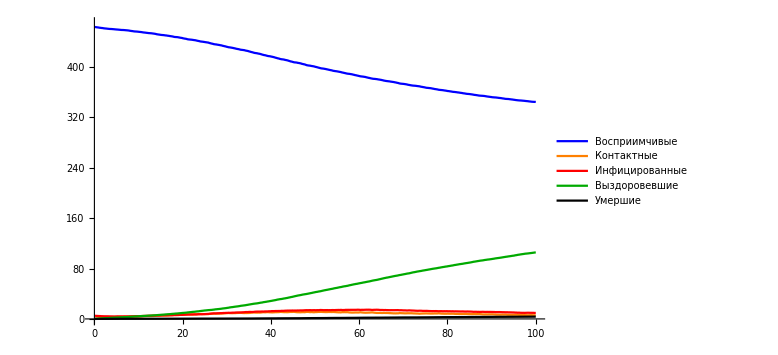

```mathematica
SEIRDplot[seird1hn5msd2m,16,10]
```

Социальная дистанция - 2 метра, время ввода меры - через неделю от начала.

```mathematica
seird1hn5msd2m7d=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5msd2m7d.m"}]];
(*seird1hn5msd2m7d=SEIRDmod[DA2[up1h5m⟦1⟧,up1h5msd2m⟦1⟧,16 7,16 93],
DA2[up1h5m⟦2⟧,up1h5msd2m⟦2⟧,16 7,16 93],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

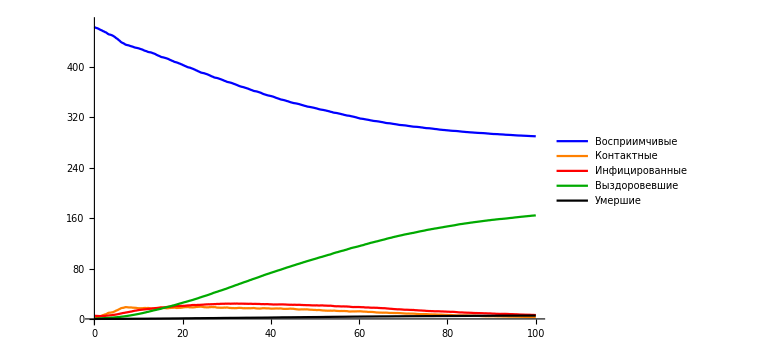

```mathematica
SEIRDplot[seird1hn5msd2m7d,16,10]
```

Социальная дистанция - 2 метра, время ввода меры - через две недели от начала.

```mathematica
seird1hn5msd2m14d=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5msd2m14d.m"}]];
(*seird1hn5msd2m14d=SEIRDmod[DA2[up1h5m⟦1⟧,up1h5msd2m⟦1⟧,16 14,16 86],
DA2[up1h5m⟦2⟧,up1h5msd2m⟦2⟧,16 14,16 86],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

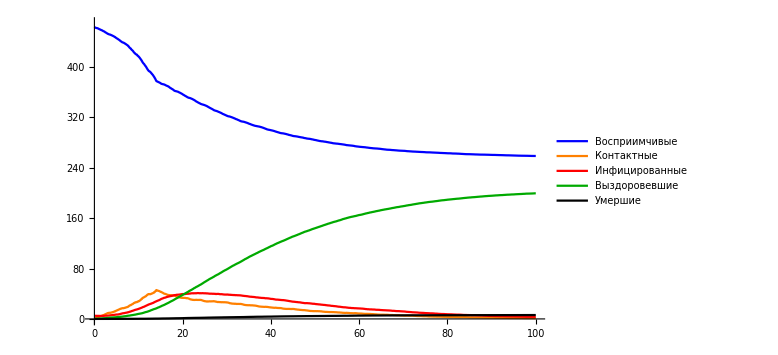

```mathematica
SEIRDplot[seird1hn5msd2m14d,16,10]
```

Социальная дистанция - 2 метра, время ввода меры - через три недели от начала.

```mathematica
seird1hn5msd2m21d=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5msd2m21d.m"}]];
(*seird1hn5msd2m21d=SEIRDmod[DA2[up1h5m⟦1⟧,up1h5msd2m⟦1⟧,16 21,16 79],
DA2[up1h5m⟦2⟧,up1h5msd2m⟦2⟧,16 21,16 79],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

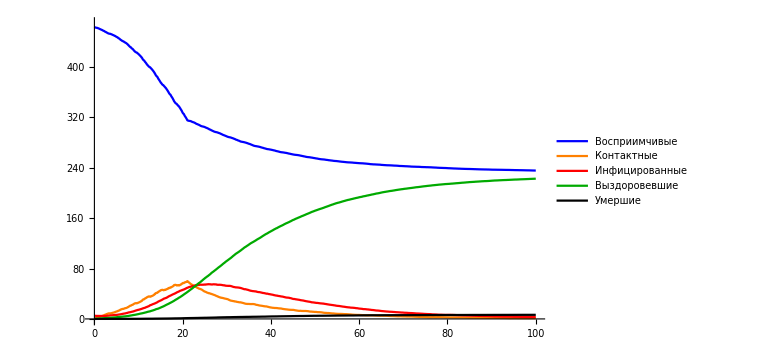

```mathematica
SEIRDplot[seird1hn5msd2m21d,16,10]
```

#### Наложение графиков

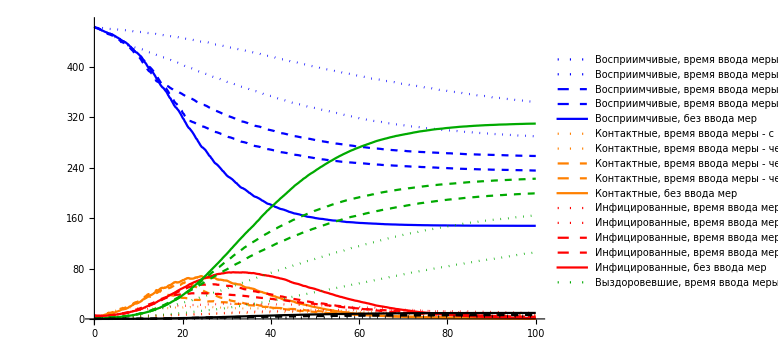

```mathematica
SEIRDplotsum[seird1hn5msd2m,seird1hn5msd2m7d,seird1hn5msd2m14d,seird1hn5msd2m21d,seird1hn5m,16,10]
```

<ТЕКСТ ПРО ВЫВОДЫ>

## Ношение масок

Рассмотрим теперь такую меру защиты как ношение масок. Эффективность этого типа защиты зависит от двух параметров: процент людей, которые носят маски и процент частиц вируса, которые она блокирует. Рассмотрим случаи, при которых ношение масок уменьшает вероятность заражения на 20, 40, 60, 80 процентов.

Ношение масок снижает вероятность заражения на 20%.

```mathematica
up1h5mwm20p=NetUnion[edgelist5m,0.8 w5m,1,Length[KDS2],12];
```

Ношение масок снижает вероятность заражения на 40%.

```mathematica
up1h5mwm40p=NetUnion[edgelist5m,0.6 w5m,1,Length[KDS2],12];
```

Ношение масок снижает вероятность заражения на 60%.

```mathematica
up1h5mwm60p=NetUnion[edgelist5m,0.4 w5m,1,Length[KDS2],12];
```

Ношение масок снижает вероятность заражения на 80%.

```mathematica
up1h5mwm80p=NetUnion[edgelist5m,0.2 w5m,1,Length[KDS2],12];
```

Ношение масок снижает вероятность заражения на 20%, время ввода меры - с первого дня.

```mathematica
seird1hn5mwm20p=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5mwm20p.m"}]];
(*seird1hn5mwm20p=SEIRDmod[DA[up1h5mwm20p⟦1⟧,16 100],
DA[up1h5mwm20p⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

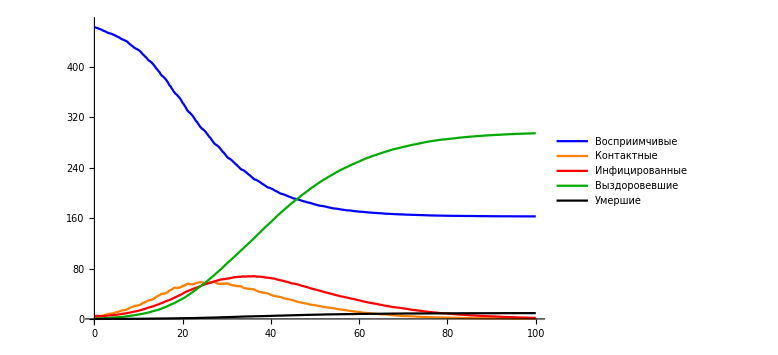

```mathematica
SEIRDplot[seird1hn5mwm20p,16,10]
```

Ношение масок снижает вероятность заражения на 20%, время ввода меры - через неделю от начала.

```mathematica
seird1hn5mwm20p7d=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5mwm20p7d.m"}]];
(*seird1hn5mwm20p7d=SEIRDmod[DA2[up1h5m⟦1⟧,up1h5mwm20p⟦1⟧,16 7,16 93],
DA2[up1h5m⟦2⟧,up1h5mwm20p⟦2⟧,16 7,16 93],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

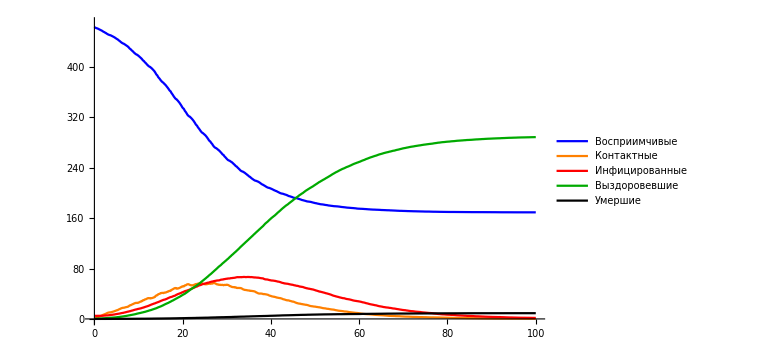

```mathematica
SEIRDplot[seird1hn5mwm20p7d,16,10]
```

Ношение масок снижает вероятность заражения на 20%, время ввода меры - через две недели от начала.

```mathematica
seird1hn5mwm20p14d=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5mwm20p14d.m"}]];
(*seird1hn5mwm20p14d=SEIRDmod[DA2[up1h5m⟦1⟧,up1h5mwm20p⟦1⟧,16 14,16 86],
DA2[up1h5m⟦2⟧,up1h5mwm20p⟦2⟧,16 14,16 86],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

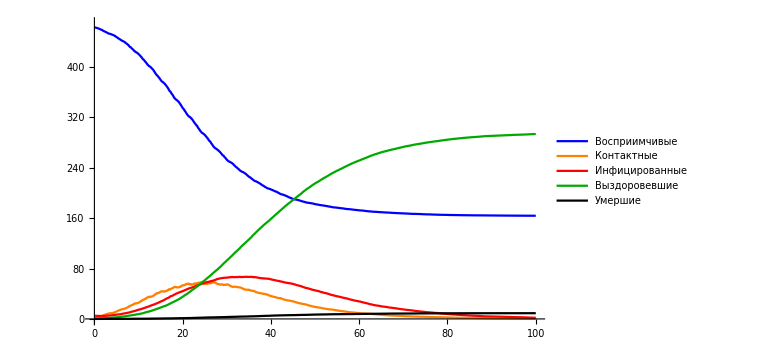

```mathematica
SEIRDplot[seird1hn5mwm20p14d,16,10]
```

Ношение масок снижает вероятность заражения на 20%, время ввода меры - через три недели от начала.

```mathematica
seird1hn5mwm20p21d=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5mwm20p21d.m"}]];
(*seird1hn5mwm20p21d=SEIRDmod[DA2[up1h5m⟦1⟧,up1h5mwm20p⟦1⟧,16 21,16 79],
DA2[up1h5m⟦2⟧,up1h5mwm20p⟦2⟧,16 21,16 79],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

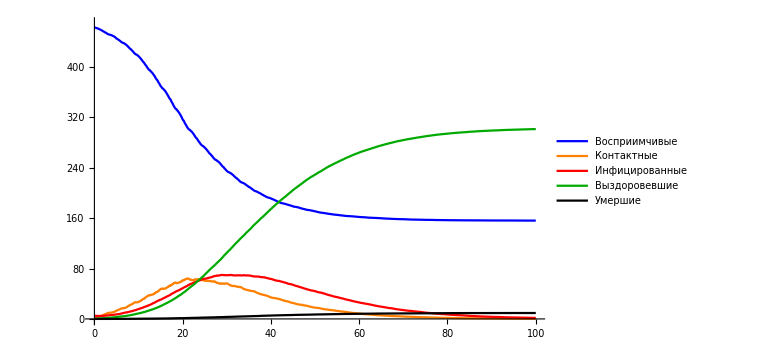

```mathematica
SEIRDplot[seird1hn5mwm20p21d,16,10]
```

#### Наложение графиков

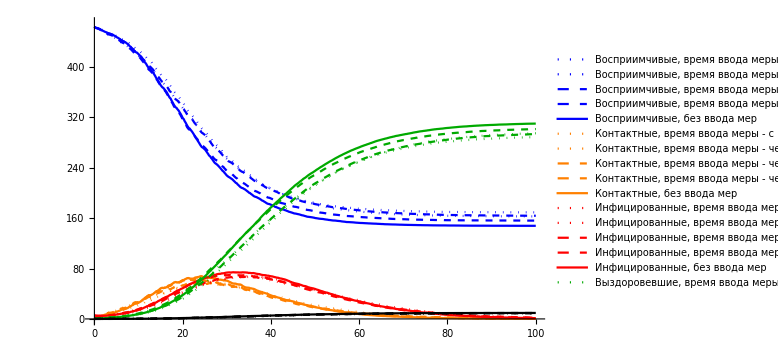

```mathematica
SEIRDplotsum[seird1hn5mwm20p,seird1hn5mwm20p7d,seird1hn5mwm20p14d,seird1hn5mwm20p21d,seird1hn5m,16,10]
```

Ношение масок снижает вероятность заражения на 40%, время ввода меры - с первого дня.

```mathematica
seird1hn5mwm40p=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5mwm40p.m"}]];
(*seird1hn5mwm40p=SEIRDmod[DA[up1h5mwm40p⟦1⟧,16 100],
DA[up1h5mwm40p⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

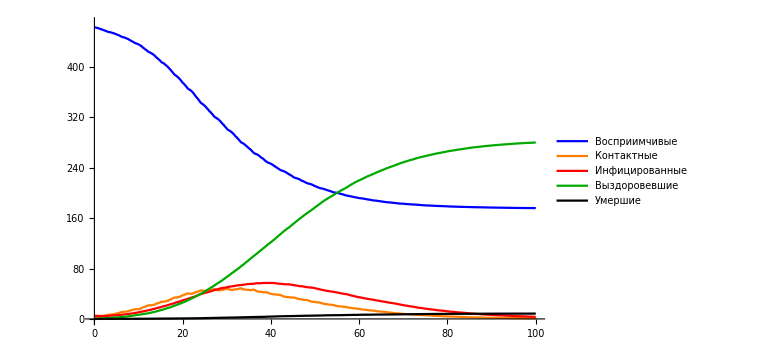

```mathematica
SEIRDplot[seird1hn5mwm40p,16,10]
```

Ношение масок снижает вероятность заражения на 40%, время ввода меры - через неделю от начала.

```mathematica
seird1hn5mwm40p7d=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5mwm40p7d.m"}]];
(*seird1hn5mwm40p7d=SEIRDmod[DA2[up1h5m⟦1⟧,up1h5mwm40p⟦1⟧,16 7,16 93],
DA2[up1h5m⟦2⟧,up1h5mwm40p⟦2⟧,16 7,16 93],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

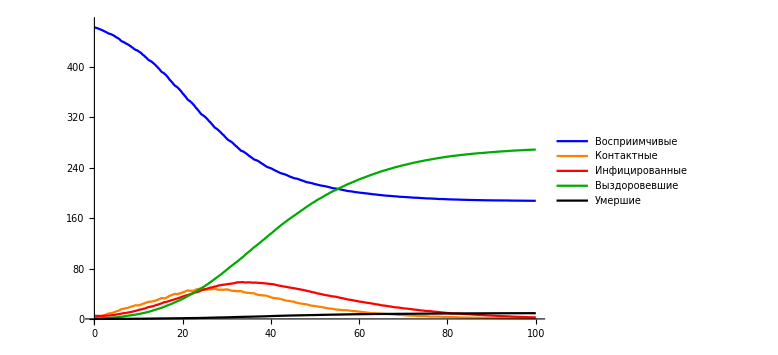

```mathematica
SEIRDplot[seird1hn5mwm40p7d,16,10]
```

Ношение масок снижает вероятность заражения на 40%, время ввода меры - через две недели от начала.

```mathematica
seird1hn5mwm40p14d=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5mwm40p14d.m"}]];
(*seird1hn5mwm40p14d=SEIRDmod[DA2[up1h5m⟦1⟧,up1h5mwm40p⟦1⟧,16 14,16 86],
DA2[up1h5m⟦2⟧,up1h5mwm40p⟦2⟧,16 14,16 86],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

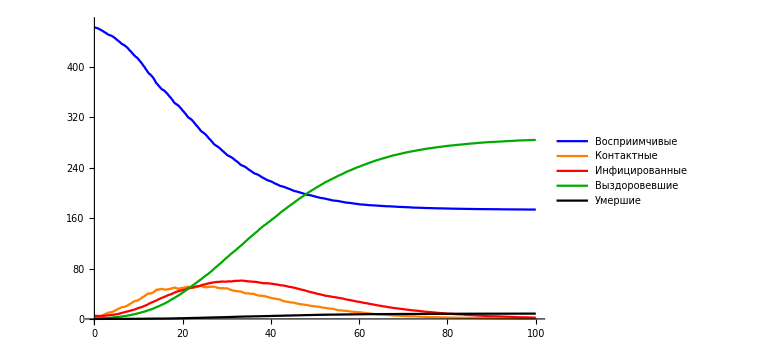

```mathematica
SEIRDplot[seird1hn5mwm40p14d,16,10]
```

Ношение масок снижает вероятность заражения на 40%, время ввода меры - через три недели от начала.

```mathematica
seird1hn5mwm40p21d=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5mwm40p21d.m"}]];
(*seird1hn5mwm40p21d=SEIRDmod[DA2[up1h5m⟦1⟧,up1h5mwm40p⟦1⟧,16 21,16 79],
DA2[up1h5m⟦2⟧,up1h5mwm40p⟦2⟧,16 21,16 79],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

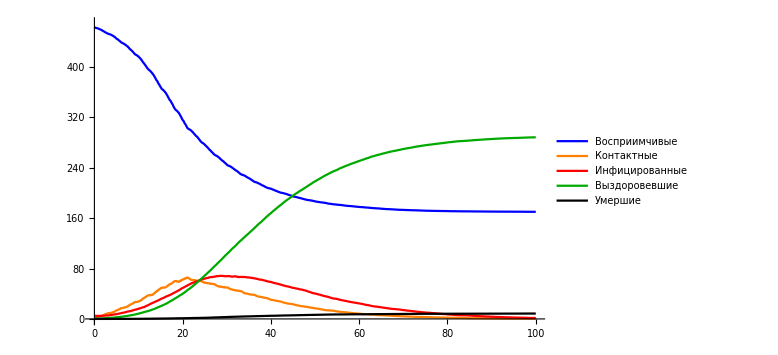

```mathematica
SEIRDplot[seird1hn5mwm40p21d,16,10]
```

#### Наложение графиков

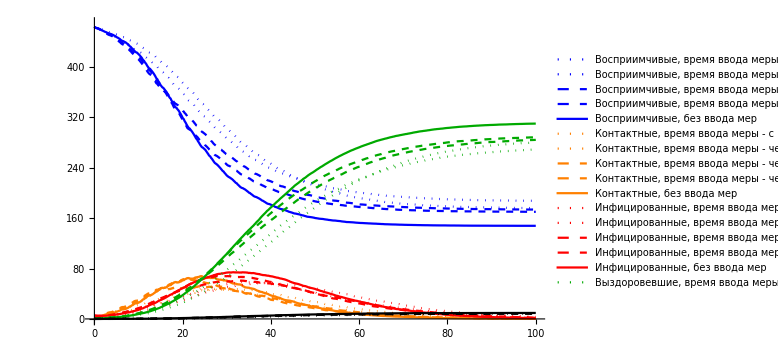

```mathematica
SEIRDplotsum[seird1hn5mwm40p,seird1hn5mwm40p7d,seird1hn5mwm40p14d,seird1hn5mwm40p21d,seird1hn5m,16,10]
```

Ношение масок снижает вероятность заражения на 60%, время ввода меры - с первого дня.

```mathematica
seird1hn5mwm60p=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5mwm60p.m"}]];
(*seird1hn5mwm60p=SEIRDmod[DA[up1h5mwm60p⟦1⟧,16 100],
DA[up1h5mwm60p⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

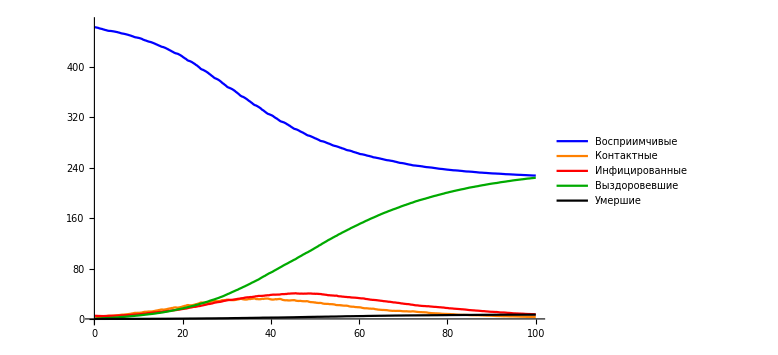

```mathematica
SEIRDplot[seird1hn5mwm60p,16,10]
```

Ношение масок снижает вероятность заражения на 60%, время ввода меры - через неделю от начала.

```mathematica
seird1hn5mwm60p7d=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5mwm60p7d.m"}]];
(*seird1hn5mwm60p7d=SEIRDmod[DA2[up1h5m⟦1⟧,up1h5mwm60p⟦1⟧,16 7,16 93],
DA2[up1h5m⟦2⟧,up1h5mwm60p⟦2⟧,16 7,16 93],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

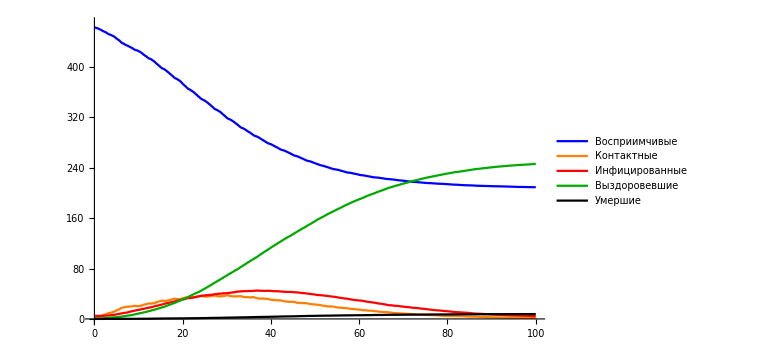

```mathematica
SEIRDplot[seird1hn5mwm60p7d,16,10]
```

Ношение масок снижает вероятность заражения на 60%, время ввода меры - через две недели от начала.

```mathematica
seird1hn5mwm60p14d=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5mwm60p14d.m"}]];
(*seird1hn5mwm60p14d=SEIRDmod[DA2[up1h5m⟦1⟧,up1h5mwm60p⟦1⟧,16 14,16 86],
DA2[up1h5m⟦2⟧,up1h5mwm60p⟦2⟧,16 14,16 86],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

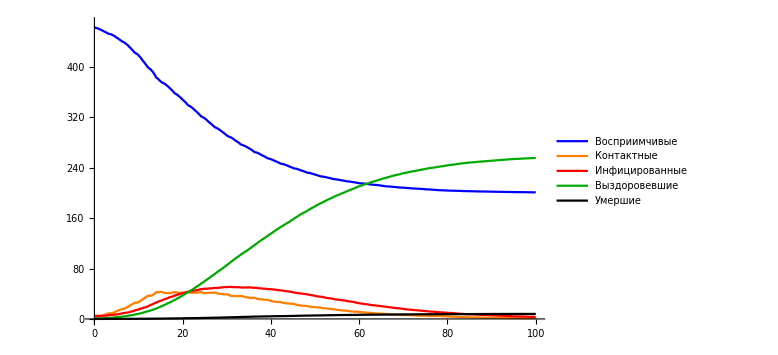

```mathematica
SEIRDplot[seird1hn5mwm60p14d,16,10]
```

Ношение масок снижает вероятность заражения на 60%, время ввода меры - через две три от начала.

```mathematica
seird1hn5mwm60p21d=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5mwm60p21d.m"}]];
(*seird1hn5mwm60p21d=SEIRDmod[DA2[up1h5m⟦1⟧,up1h5mwm60p⟦1⟧,16 21,16 79],
DA2[up1h5m⟦2⟧,up1h5mwm60p⟦2⟧,16 21,16 79],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

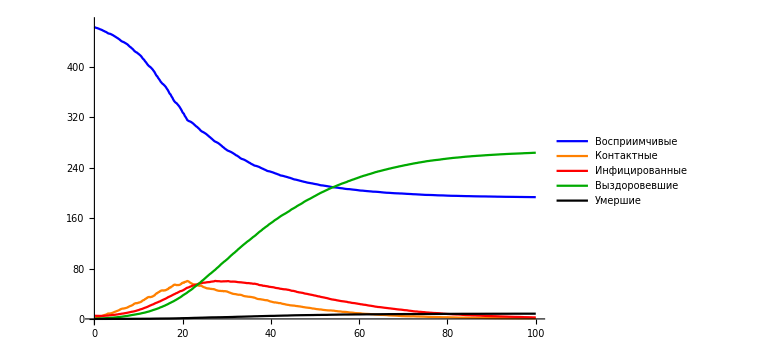

```mathematica
SEIRDplot[seird1hn5mwm60p21d,16,10]
```

#### Наложение графиков

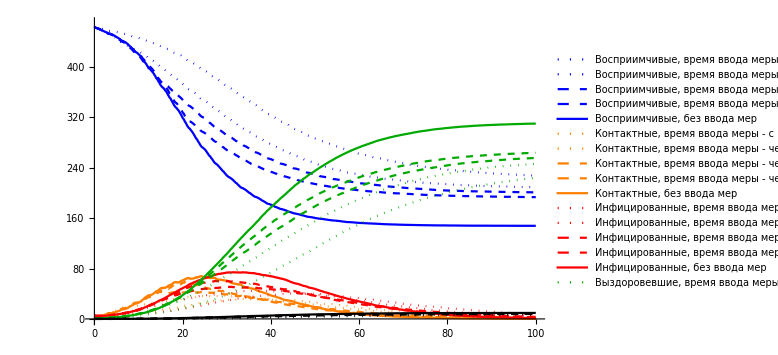

```mathematica
SEIRDplotsum[seird1hn5mwm60p,seird1hn5mwm60p7d,seird1hn5mwm60p14d,seird1hn5mwm60p21d,seird1hn5m,16,10]
```

Ношение масок снижает вероятность заражения на 80%, время ввода меры - с первого дня.

```mathematica
seird1hn5mwm80p=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5mwm80p.m"}]];
(*seird1hn5mwm80p=SEIRDmod[DA[up1h5mwm80p⟦1⟧,16 100],
DA[up1h5mwm80p⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

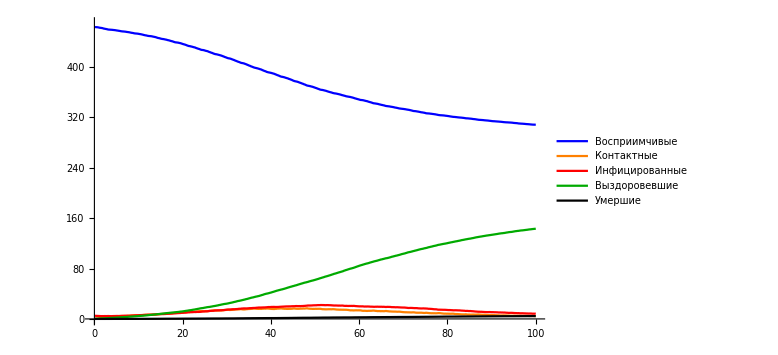

```mathematica
SEIRDplot[seird1hn5mwm80p,16,10]
```

Ношение масок снижает вероятность заражения на 80%, время ввода меры - через неделю от начала.

```mathematica
seird1hn5mwm80p7d=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5mwm80p7d.m"}]];
(*seird1hn5mwm80p7d=SEIRDmod[DA2[up1h5m⟦1⟧,up1h5mwm80p⟦1⟧,16 7,16 93],
DA2[up1h5m⟦2⟧,up1h5mwm80p⟦2⟧,16 7,16 93],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

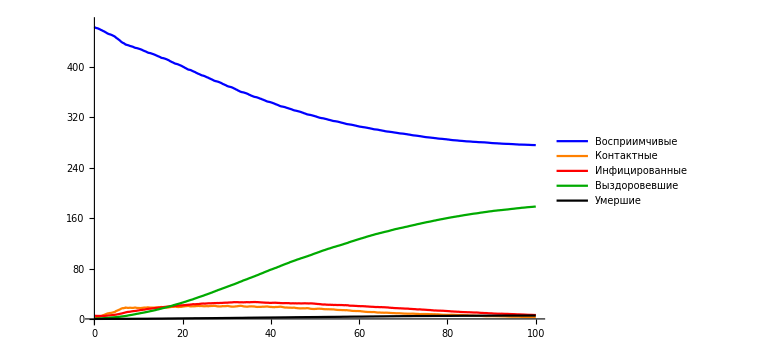

```mathematica
SEIRDplot[seird1hn5mwm80p7d,16,10]
```

Ношение масок снижает вероятность заражения на 80%, время ввода меры - через две недели от начала.

```mathematica
seird1hn5mwm80p14d=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5mwm80p14d.m"}]];
(*seird1hn5mwm80p14d=SEIRDmod[DA2[up1h5m⟦1⟧,up1h5mwm80p⟦1⟧,16 14,16 86],
DA2[up1h5m⟦2⟧,up1h5mwm80p⟦2⟧,16 14,16 86],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

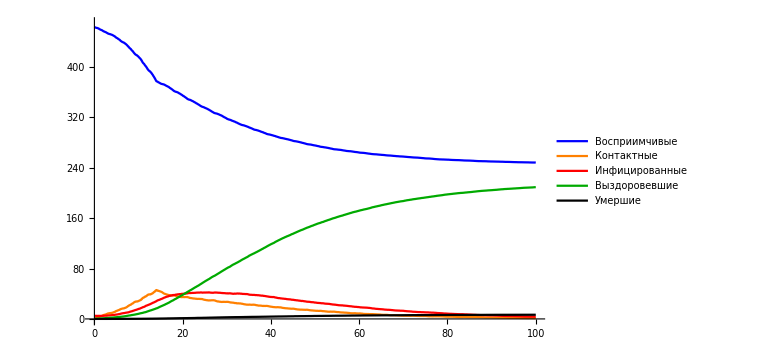

```mathematica
SEIRDplot[seird1hn5mwm80p14d,16,10]
```

Ношение масок снижает вероятность заражения на 80%, время ввода меры - через три недели от начала.

```mathematica
seird1hn5mwm80p21d=Import[FileNameJoin[{NotebookDirectory[],"seird1hn5mwm80p21d.m"}]];
(*seird1hn5mwm80p21d=SEIRDmod[DA2[up1h5m⟦1⟧,up1h5mwm80p⟦1⟧,16 21,16 79],
DA2[up1h5m⟦2⟧,up1h5mwm80p⟦2⟧,16 21,16 79],vertexcount,5,1,ϵ1h,γ1h,0.03,100];*)
```

#### График

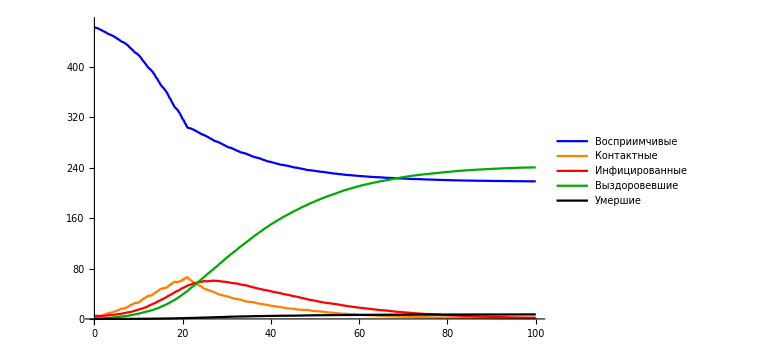

```mathematica
SEIRDplot[seird1hn5mwm80p21d,16,10]
```

#### Наложение графиков

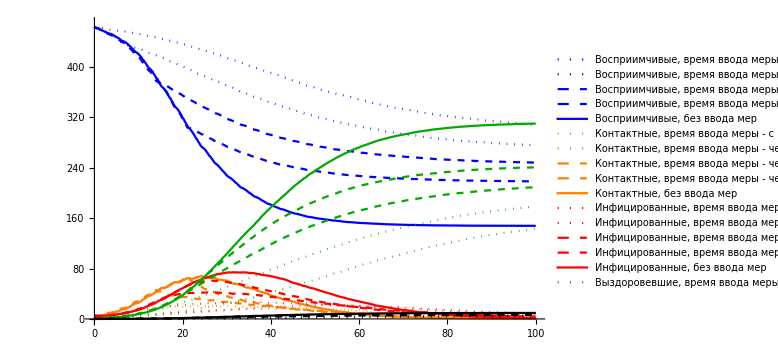

```mathematica
SEIRDplotsum[seird1hn5mwm80p,seird1hn5mwm80p7d,seird1hn5mwm80p14d,seird1hn5mwm80p21d,seird1hn5m,16,10]
```

## Тестирование и карантинные меры

<ТЕКСТ>

#### График перехода состояний в SEIRDQ модели

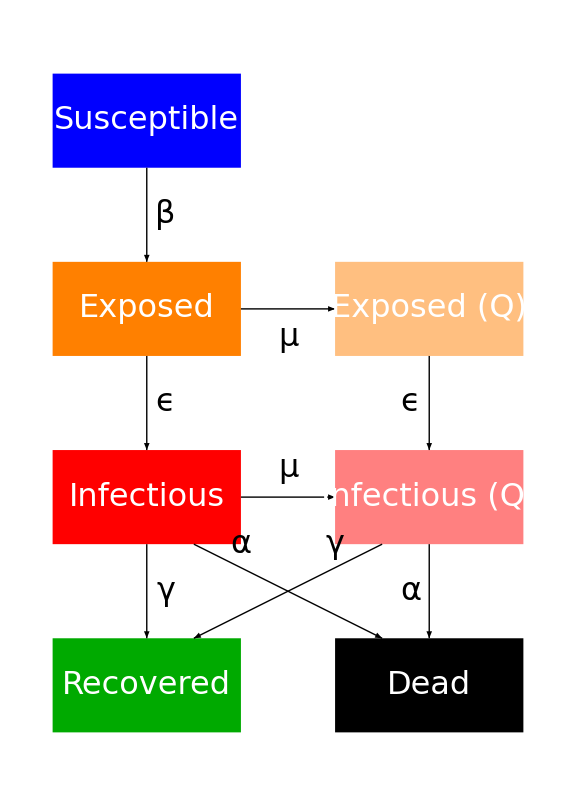

```mathematica
Graphics[{Blue,Rectangle[{0,0},{2,-1},RoundingRadius->1/3],
White,Text[Style["Susceptible",32],{1,-1/2}],Orange,Rectangle[{0,-2},{2,-3},RoundingRadius->1/3],
White,Text[Style["Exposed",32],{1,-5/2}],Lighter[Orange,.5],
Rectangle[{3,-2},{5,-3},RoundingRadius->1/3],White,Text[Style["Exposed (Q)",32],{4,-5/2}],
Red,Rectangle[{0,-4},{2,-5},RoundingRadius->1/3],White,Text[Style["Infectious",32],{1,-9/2}],
Lighter[Red,.5],Rectangle[{3,-4},{5,-5},RoundingRadius->1/3],White,
Text[Style["Infectious (Q)",32],{4,-9/2}],Darker[Green],Rectangle[{0,-6},{2,-7},RoundingRadius->1/3],
White,Text[Style["Recovered",32],{1,-13/2}],Black,Rectangle[{3,-6},{5,-7},RoundingRadius->1/3],
White,Text[Style["Dead",32],{4,-13/2}],Black,Arrow[{{1,-1},{1,-2}}],Arrow[{{1,-3},{1,-4}}],
Arrow[{{1,-5},{1,-6}}],Arrow[{{2,-5/2},{3,-5/2}}],Arrow[{{2,-9/2},{3,-9/2}}],Arrow[{{4,-3},{4,-4}}],
Arrow[{{4,-5},{4,-6}}],Arrow[{{3/2,-5},{7/2,-6}}],Arrow[{{7/2,-5},{3/2,-6}}],
Text[Style["β",32],{6/5,-3/2}],Text[Style["ϵ",32],{6/5,-7/2}],Text[Style["γ",32],{6/5,-11/2}],
Text[Style["ϵ",32],{19/5,-7/2}],Text[Style["α",32],{19/5,-11/2}],Text[Style["μ",32],{5/2,-14/5}],
Text[Style["μ",32],{5/2,-21/5}],Text[Style["α",32],{2,-5}],Text[Style["γ",32],{3,-5}]},
ImageSize->Large]
```

<ТЕКСТ>

```mathematica
SEIRDQ[ele_,ewe_,vc_,i0_,β_,ϵ_,γ_,α_,tr_,trf_,ts_]:=
Module[{ntr=Round[tr vc],predata=Table[NearestNeighborList[ele⟦i⟧,ewe⟦i⟧,vc],{i,1,Length[ele]}],
data=Table[{i,"Susceptible",{},{}},{j,1,Length[ele]},{i,1,vc}],ev={},iv={},rv={},dv={},tv={},
eqv={},iqv={}},Do[Do[data⟦i,j,3⟧=predata⟦i,j,1⟧;data⟦i,j,4⟧=predata⟦i,j,2⟧,{j,1,vc}],
{i,1,Length[ele]}];iv=RandomSample[Range[vc],i0];Do[data⟦1,iv⟦i⟧,2⟧="Infected",{i,1,i0}];
Do[rv=Cases[data⟦i⟧,{_,"Recovered",_,_}];If[rv≠{},Do[data⟦i+1,rv⟦j,1⟧,2⟧="Recovered",
{j,1,Length[rv]}]];dv=Cases[data⟦i⟧,{_,"Dead",_,_}];If[dv≠{},Do[data⟦i+1,dv⟦j,1⟧,2⟧="Dead",
{j,1,Length[dv]}]];ev=Cases[data⟦i⟧,{_,"Exposed",_,_}];iv=Cases[data⟦i⟧,{_,"Infected",_,_}];
eqv=Cases[data⟦i⟧,{_,"Exposed (quarantine)",_,_}];
iqv=Cases[data⟦i⟧,{_,"Infected (quarantine)",_,_}];
If[ev≠{},Do[If[RandomChoice[{ϵ,1-ϵ}->{True,False}]==True,data⟦i+1,ev⟦j,1⟧,2⟧="Infected",
data⟦i+1,ev⟦j,1⟧,2⟧="Exposed"],{j,1,Length[ev]}]];
If[eqv≠{},Do[If[RandomChoice[{ϵ,1-ϵ}->{True,False}]==True,
data⟦i+1,eqv⟦j,1⟧,2⟧="Infected (quarantine)",data⟦i+1,eqv⟦j,1⟧,2⟧="Exposed (quarantine)"],
{j,1,Length[eqv]}]];If[iqv≠{},Do[If[RandomChoice[{γ,1-γ}->{True,False}]==True,
If[RandomChoice[{α,1-α}->{True,False}]==True,data⟦i+1,iqv⟦j,1⟧,2⟧="Dead",
data⟦i+1,iqv⟦j,1⟧,2⟧="Recovered"],data⟦i+1,iqv⟦j,1⟧,2⟧="Infected (quarantine)"],
{j,1,Length[iqv]}]];If[iv≠{},Do[If[iv⟦j,3⟧≠{},
Do[If[RandomChoice[{β iv⟦j,4,k⟧,1-β iv⟦j,4,k⟧}->{True,False}]==True,
If[data⟦i,iv⟦j,3,k⟧,2⟧=="Susceptible",data⟦i+1,iv⟦j,3,k⟧,2⟧="Exposed"]],{k,1,Length[iv⟦j,3⟧]}]];
If[RandomChoice[{γ,1-γ}->{True,False}]==True,If[RandomChoice[{α,1-α}->{True,False}]==True,
data⟦i+1,iv⟦j,1⟧,2⟧="Dead",data⟦i+1,iv⟦j,1⟧,2⟧="Recovered"],data⟦i+1,iv⟦j,1⟧,2⟧="Infected"],
{j,1,Length[iv]}]];If[Mod[i+1,trf]==0&&i+1≥ts,
tv=Flatten[{Cases[data⟦i⟧,{_,"Susceptible",_,_}]⟦All,1⟧,
Cases[data⟦i⟧,{_,"Exposed",_,_}]⟦All,1⟧,Cases[data⟦i⟧,{_,"Infected",_,_}]⟦All,1⟧}];
tv=RandomSample[tv,If[Length[tv]>ntr,ntr,Length[tv]]];Do[If[data⟦i,tv⟦j⟧,2⟧=="Exposed",
data⟦i+1,tv⟦j⟧,2⟧="Exposed (quarantine)"];If[data⟦i,tv⟦j⟧,2⟧=="Infected",
data⟦i+1,tv⟦j⟧,2⟧="Infected (quarantine)"],{j,1,Length[tv]}]],{i,1,Length[ele]-1}];data]
```

Вспомогательная функция для моделирования.

```mathematica
SEIRDQmod[ele_,ewe_,vc_,i0_,β_,ϵ_,γ_,α_,tr_,trf_,ts_,n_]:=
Mean[Table[Module[{out=SEIRDQ[ele,ewe,vc,i0,β,ϵ,γ,α,tr,trf,ts,α]},
Table[{Length[Cases[out⟦i⟧,{_,"Susceptible",_,_}]],
Length[Cases[out⟦i⟧,{_,"Exposed",_,_}]],Length[Cases[out⟦i⟧,{_,"Exposed (quarantine)",_,_}]],
Length[Cases[out⟦i⟧,{_,"Infected",_,_}]],Length[Cases[out⟦i⟧,{_,"Infected (quarantine)",_,_}]],
Length[Cases[out⟦i⟧,{_,"Recovered",_,_}]],Length[Cases[out⟦i⟧,{_,"Dead",_,_}]]},
{i,1,Length[out]}]],{l,1,n}]]
```

Вспомогательная функция для построения графиков.

```mathematica
SEIRDQplot[data_,dt1_,dt2_]:=ListLinePlot[Table[{j,data⟦j,i⟧},{i,1,7},{j,1,Length[data]}],
PlotRange->{{0,Length[data]},{0,Total[data⟦1⟧]}},
Ticks->{Table[{dt1 i,i},{i,0,Round[Length[data]/dt1],dt2}],Automatic},
PlotLegends->Placed[{"Восприимчивые","Контактные","Контактные на карантине","Инфицированные",
"Инфицированные на карантине","Выздоровевшие","Умершие"},Bottom],
PlotStyle->{Blue,Orange,Lighter[Orange,.5],Red,Lighter[Red,.5],Darker[Green],Black},ImageSize->Large]
```

Вспомогательная функция для построения графиков .

```mathematica
SEIRDQplotsum[o1_,o2_,o3_,o4_,o5_,dt1_,dt2_]:=
ListLinePlot[Module[{n=Length[o1]},{Table[{i,o1⟦i,1⟧},{i,1,n}],Table[{i,o2⟦i,1⟧},{i,1,n}],
Table[{i,o3⟦i,1⟧},{i,1,n}],Table[{i,o4⟦i,1⟧},{i,1,n}],Table[{i,o5⟦i,1⟧},{i,1,n}],
Table[{i,o1⟦i,2⟧},{i,1,n}],Table[{i,o2⟦i,2⟧},{i,1,n}],Table[{i,o3⟦i,2⟧},{i,1,n}],
Table[{i,o4⟦i,2⟧},{i,1,n}],Table[{i,o5⟦i,2⟧},{i,1,n}],Table[{i,o1⟦i,3⟧},{i,1,n}],
Table[{i,o2⟦i,3⟧},{i,1,n}],Table[{i,o3⟦i,3⟧},{i,1,n}],Table[{i,o4⟦i,3⟧},{i,1,n}],
Table[{i,o1⟦i,4⟧},{i,1,n}],Table[{i,o2⟦i,4⟧},{i,1,n}],Table[{i,o3⟦i,4⟧},{i,1,n}],
Table[{i,o4⟦i,4⟧},{i,1,n}],Table[{i,o5⟦i,3⟧},{i,1,n}],Table[{i,o1⟦i,5⟧},{i,1,n}],
Table[{i,o2⟦i,5⟧},{i,1,n}],Table[{i,o3⟦i,5⟧},{i,1,n}],Table[{i,o4⟦i,5⟧},{i,1,n}],
Table[{i,o1⟦i,6⟧},{i,1,n}],Table[{i,o2⟦i,6⟧},{i,1,n}],Table[{i,o3⟦i,6⟧},{i,1,n}],
Table[{i,o4⟦i,6⟧},{i,1,n}],Table[{i,o5⟦i,4⟧},{i,1,n}],Table[{i,o1⟦i,7⟧},{i,1,n}],
Table[{i,o2⟦i,7⟧},{i,1,n}],Table[{i,o3⟦i,7⟧},{i,1,n}],Table[{i,o4⟦i,7⟧},{i,1,n}],
Table[{i,o5⟦i,5⟧},{i,1,n}]}],PlotRange->{{0,Length[o1]},{0,Total[o1⟦1⟧]}},
Ticks->{Table[{dt1 i,i},{i,0,Round[Length[o1]/dt1],dt2}],Automatic},
PlotStyle->{{Blue,Dotted},{Blue,Dotted,Thick},{Blue,Dashed},{Blue,Dashed,Thick},{Blue,Thick},
{Orange,Dotted},{Orange,Dotted,Thick},{Orange,Dashed},{Orange,Dashed,Thick},{Orange,Thick},
{Lighter[Orange,.5],Dotted},{Lighter[Orange,.5],Dotted,Thick},
{Lighter[Orange,.5],Dashed},{Lighter[Orange,.5],Dashed,Thick},
{Red,Dotted},{Red,Dotted,Thick},{Red,Dashed},{Red,Dashed,Thick},{Red,Thick},
{Lighter[Red,.5],Dotted},{Lighter[Red,.5],Dotted,Thick},
{Lighter[Red,.5],Dashed},{Lighter[Red,.5],Dashed,Thick},
{Darker[Green],Dotted},{Darker[Green],Dotted,Thick},{Darker[Green],Dashed},
{Darker[Green],Dashed,Thick},{Darker[Green],Thick},
{Black,Dotted},{Black,Dotted,Thick},{Black,Dashed},{Black,Dashed,Thick},{Black,Thick}},
PlotLegends->Placed[LineLegend[{"Восприимчивые, время ввода меры - с первого дня",
"Восприимчивые, время ввода меры - через неделю от начала",
"Восприимчивые, время ввода меры - через две недели от начала",
"Восприимчивые, время ввода меры - через три недели от начала",
"Восприимчивые, без ввода мер","Контактные, время ввода меры - с первого дня",
"Контактные, время ввода меры - через неделю от начала",
"Контактные, время ввода меры - через две недели от начала",
"Контактные, время ввода меры - через три недели от начала",
"Контактные, без ввода мер","Контактные на карантине, время ввода меры - с первого дня",
"Контактные на карантине, время ввода меры - через неделю от начала",
"Контактные на карантине, время ввода меры - через две недели от начала",
"Контактные на карантине, время ввода меры - через три недели от начала",
"Инфицированные, время ввода меры - с первого дня",
"Инфицированные, время ввода меры - через неделю от начала",
"Инфицированные, время ввода меры - через две недели от начала",
"Инфицированные, время ввода меры - через три недели от начала",
"Инфицированные, без ввода мер",
"Инфицированные на карантине, время ввода меры - с первого дня",
"Инфицированные на карантине, время ввода меры - через неделю от начала",
"Инфицированные на карантине, время ввода меры - через две недели от начала",
"Инфицированные на карантине, время ввода меры - через три недели от начала",
"Выздоровевшие, время ввода меры - с первого дня",
"Выздоровевшие, время ввода меры - через неделю от начала",
"Выздоровевшие, время ввода меры - через две недели от начала",
"Выздоровевшие, время ввода меры - через три недели от начала",
"Выздоровевшие, без ввода мер","Умершие, время ввода меры - с первого дня",
"Умершие, время ввода меры - через неделю от начала",
"Умершие, время ввода меры - через две недели от начала",
"Умершие, время ввода меры - через три недели от начала",
"Умершие, без ввода мер"},LegendLayout->{"Column", 1}],Bottom],ImageSize->Large]
```

Уровень тестирования от населения - 1%, время ввода меры - с первого дня.

```mathematica
seirdq1hn5mtr1p=Import[FileNameJoin[{NotebookDirectory[],"seirdq1hn5mtr1p.m"}]];
(*seirdq1hn5mtr1p=SEIRDmod[DA[up1h5m⟦1⟧,16 100],
DA[up1h5m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,0.01,16,15,100];*)
```

#### График

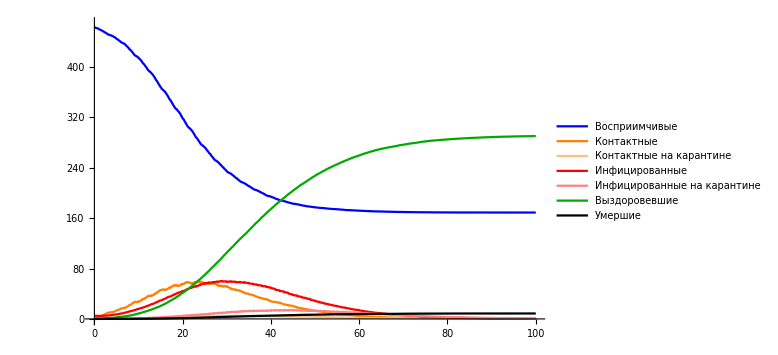

```mathematica
SEIRDQplot[seirdq1hn5mtr1p,16,10]
```

Уровень тестирования от населения - 1%, время ввода меры - через неделю от начала.

```mathematica
seirdq1hn5mtr1p7d=Import[FileNameJoin[{NotebookDirectory[],"seirdq1hn5mtr1p7d.m"}]];
(*seirdq1hn5mtr1p7d=SEIRDmod[DA[up1h5m⟦1⟧,16 100],
DA[up1h5m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,0.01,16,15+16 6,100];*)
```

#### График

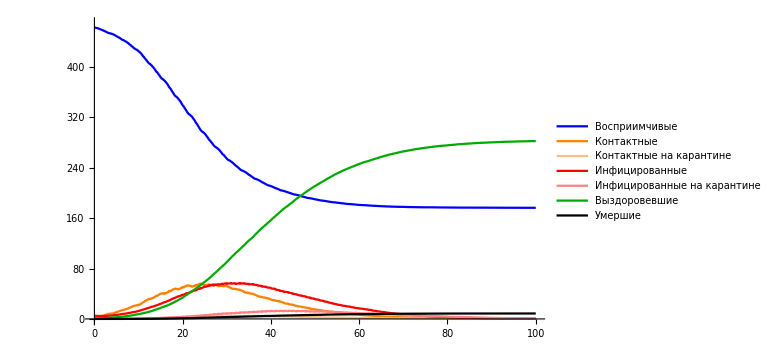

```mathematica
SEIRDQplot[seirdq1hn5mtr1p7d,16,10]
```

Уровень тестирования от населения - 1%, время ввода меры - через две недели от начала.

```mathematica
seirdq1hn5mtr1p14d=Import[FileNameJoin[{NotebookDirectory[],"seirdq1hn5mtr1p14d.m"}]];
(*seirdq1hn5mtr1p14d=SEIRDmod[DA[up1h5m⟦1⟧,16 100],
DA[up1h5m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,0.01,16,15+16 13,100];*)
```

#### График

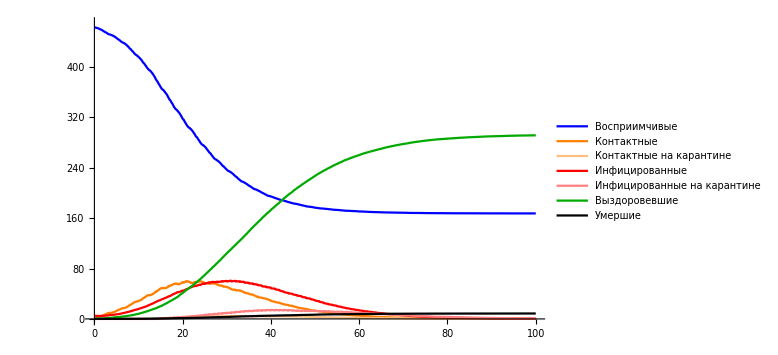

```mathematica
SEIRDQplot[seirdq1hn5mtr1p14d,16,10]
```

Уровень тестирования от населения - 1%, время ввода меры - через три недели от начала.

```mathematica
seirdq1hn5mtr1p21d=Import[FileNameJoin[{NotebookDirectory[],"seirdq1hn5mtr1p21d.m"}]];
(*seirdq1hn5mtr1p21d=SEIRDmod[DA[up1h5m⟦1⟧,16 100],
DA[up1h5m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,0.01,16,15+16 20,100];*)
```

#### График

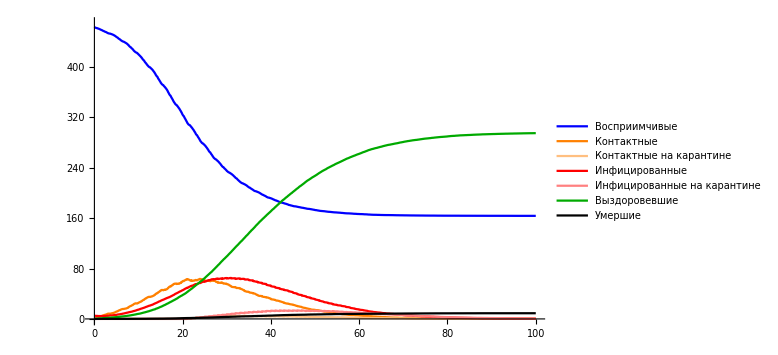

```mathematica
SEIRDQplot[seirdq1hn5mtr1p21d,16,10]
```

#### Наложение графиков

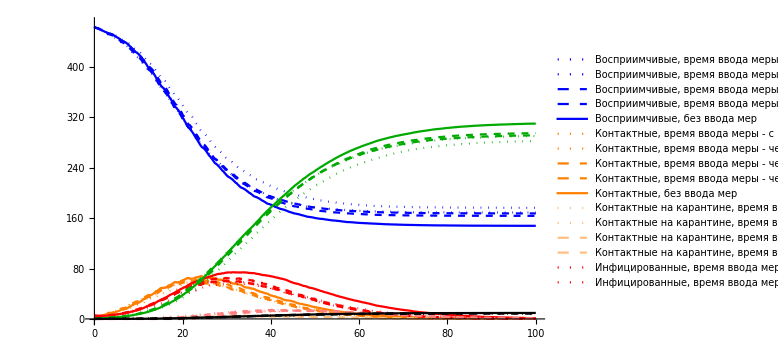

```mathematica
SEIRDQplotsum[seirdq1hn5mtr1p,seirdq1hn5mtr1p7d,seirdq1hn5mtr1p14d,
seirdq1hn5mtr1p21d,seird1hn5m,16,10]
```

Уровень тестирования от населения - 2%, время ввода меры - с первого дня.

```mathematica
seirdq1hn5mtr2p=Import[FileNameJoin[{NotebookDirectory[],"seirdq1hn5mtr2p.m"}]];
(*seirdq1hn5mtr2p=SEIRDmod[DA[up1h5m⟦1⟧,16 100],
DA[up1h5m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,0.02,16,15,100];*)
```

#### График

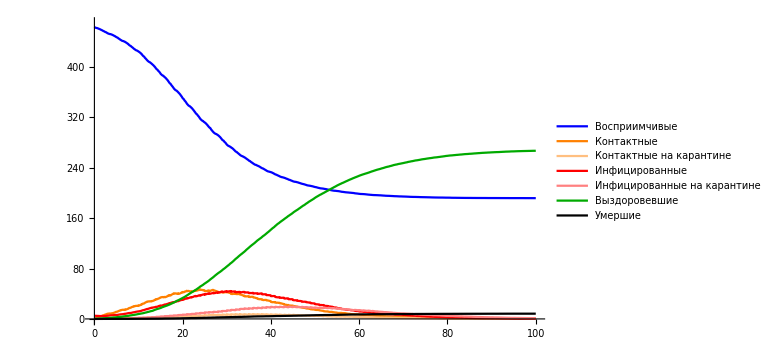

```mathematica
SEIRDQplot[seirdq1hn5mtr2p,16,10]
```

Уровень тестирования от населения - 2%, время ввода меры - через неделю от начала.

```mathematica
seirdq1hn5mtr2p7d=Import[FileNameJoin[{NotebookDirectory[],"seirdq1hn5mtr2p7d.m"}]];
(*seirdq1hn5mtr2p7d=SEIRDmod[DA[up1h5m⟦1⟧,16 100],
DA[up1h5m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,0.02,16,15+16 6,100];*)
```

#### График

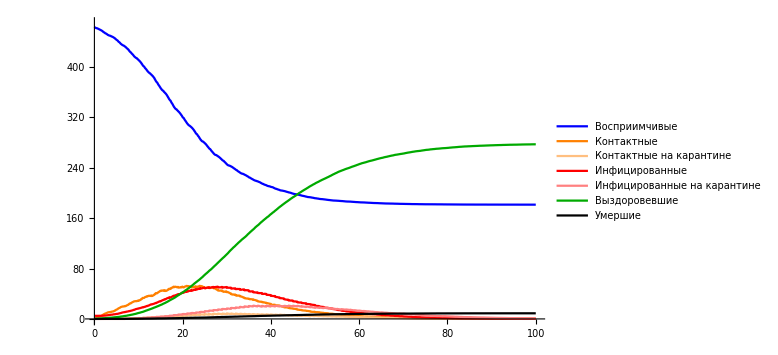

```mathematica
SEIRDQplot[seirdq1hn5mtr2p7d,16,10]
```

Уровень тестирования от населения - 2%, время ввода меры - через две недели от начала.

```mathematica
seirdq1hn5mtr2p14d=Import[FileNameJoin[{NotebookDirectory[],"seirdq1hn5mtr2p14d.m"}]];
(*seirdq1hn5mtr2p14d=SEIRDmod[DA[up1h5m⟦1⟧,16 100],
DA[up1h5m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,0.02,16,15+16 13,100];*)
```

#### График

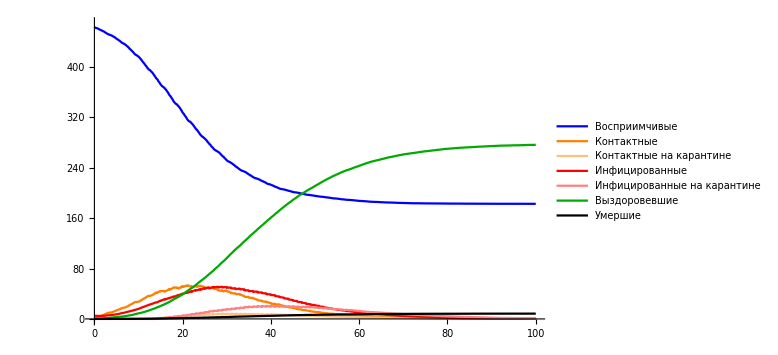

```mathematica
SEIRDQplot[seirdq1hn5mtr2p14d,16,10]
```

Уровень тестирования от населения - 2%, время ввода меры - через три недели от начала.

```mathematica
seirdq1hn5mtr2p21d=Import[FileNameJoin[{NotebookDirectory[],"seirdq1hn5mtr2p21d.m"}]];
(*seirdq1hn5mtr2p21d=SEIRDmod[DA[up1h5m⟦1⟧,16 100],
DA[up1h5m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,0.02,16,15+16 20,100];*)
```

#### График

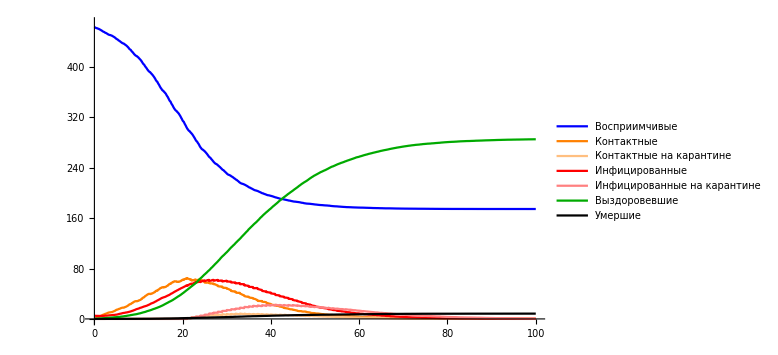

```mathematica
SEIRDQplot[seirdq1hn5mtr2p21d,16,10]
```

#### Наложение графиков

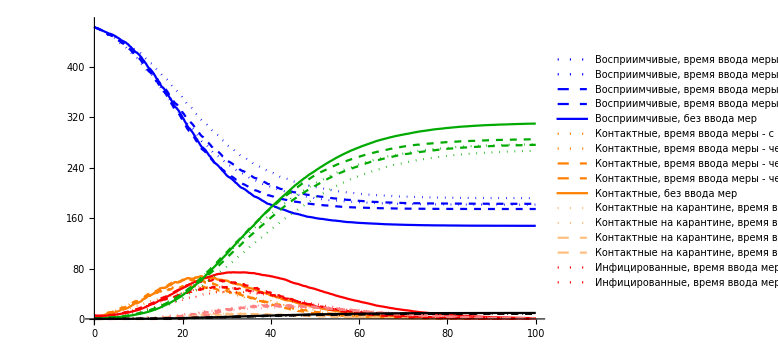

```mathematica
SEIRDQplotsum[seirdq1hn5mtr2p,seirdq1hn5mtr2p7d,seirdq1hn5mtr2p14d,
seirdq1hn5mtr2p21d,seird1hn5m,16,10]
```

Уровень тестирования от населения - 5%, время ввода меры - с первого дня.

```mathematica
seirdq1hn5mtr5p=Import[FileNameJoin[{NotebookDirectory[],"seirdq1hn5mtr5p.m"}]];
(*seirdq1hn5mtr5p=SEIRDmod[DA[up1h5m⟦1⟧,16 100],
DA[up1h5m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,0.05,16,15,100];*)
```

#### График

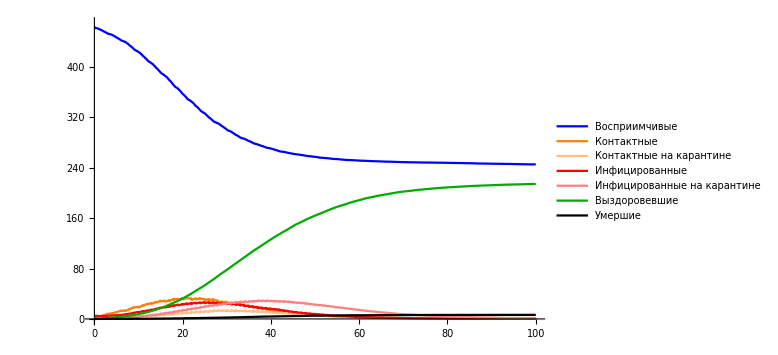

```mathematica
SEIRDQplot[seirdq1hn5mtr5p,16,10]
```

Уровень тестирования от населения - 5%, время ввода меры - через неделю от начала.

```mathematica
seirdq1hn5mtr5p7d=Import[FileNameJoin[{NotebookDirectory[],"seirdq1hn5mtr5p7d.m"}]];
(*seirdq1hn5mtr5p7d=SEIRDmod[DA[up1h5m⟦1⟧,16 100],
DA[up1h5m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,0.05,16,15+16 6,100];*)
```

#### График

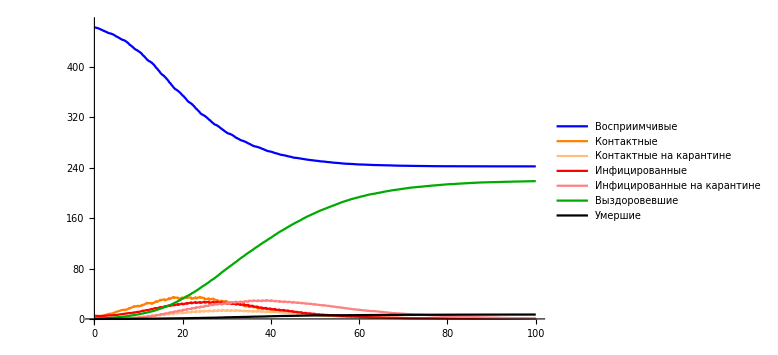

```mathematica
SEIRDQplot[seirdq1hn5mtr5p7d,16,10]
```

Уровень тестирования от населения - 5%, время ввода меры - через две недели от начала.

```mathematica
seirdq1hn5mtr5p14d=Import[FileNameJoin[{NotebookDirectory[],"seirdq1hn5mtr5p14d.m"}]];
(*seirdq1hn5mtr5p14d=SEIRDmod[DA[up1h5m⟦1⟧,16 100],
DA[up1h5m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,0.05,16,15+16 13,100];*)
```

#### График

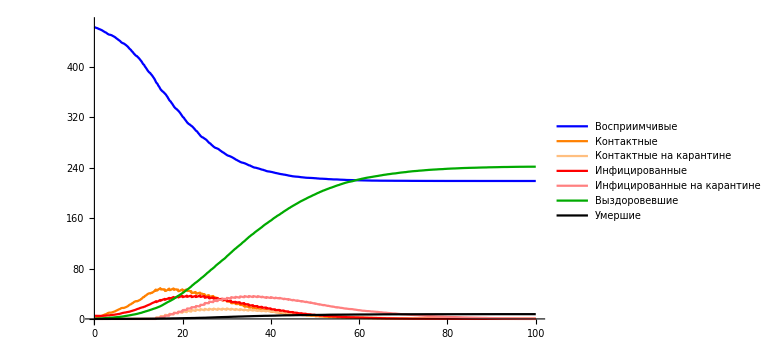

```mathematica
SEIRDQplot[seirdq1hn5mtr5p14d,16,10]
```

Уровень тестирования от населения - 5%, время ввода меры - через три недели от начала.

```mathematica
seirdq1hn5mtr5p21d=Import[FileNameJoin[{NotebookDirectory[],"seirdq1hn5mtr5p21d.m"}]];
(*seirdq1hn5mtr5p21d=SEIRDmod[DA[up1h5m⟦1⟧,16 100],
DA[up1h5m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,0.05,16,15+16 20,100];*)
```

#### График

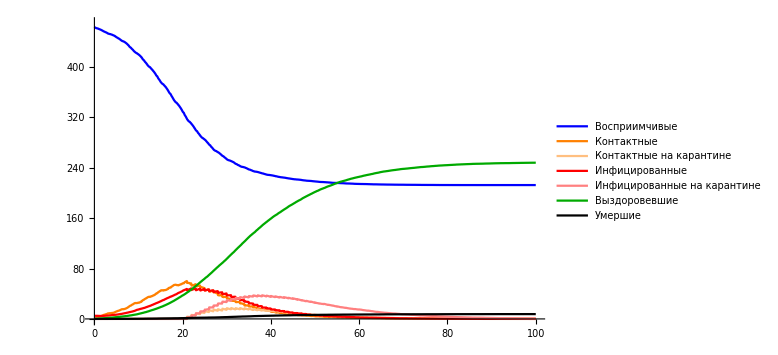

```mathematica
SEIRDQplot[seirdq1hn5mtr5p21d,16,10]
```

#### Наложение графиков

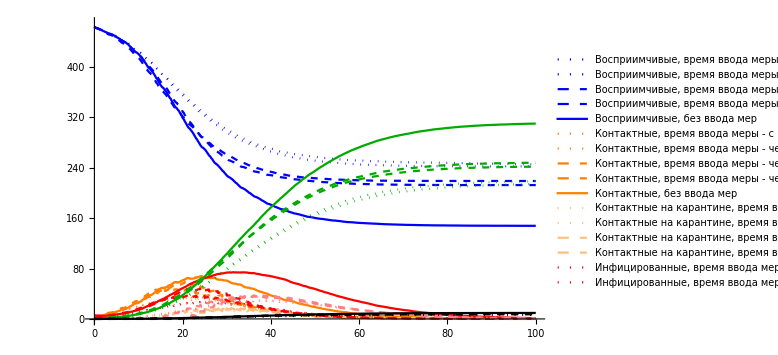

```mathematica
SEIRDQplotsum[seirdq1hn5mtr5p,seirdq1hn5mtr5p7d,seirdq1hn5mtr5p14d,
seirdq1hn5mtr5p21d,seird1hn5m,16,10]
```

Уровень тестирования от населения - 10%, время ввода меры - с первого дня.

```mathematica
seirdq1hn5mtr10p=Import[FileNameJoin[{NotebookDirectory[],"seirdq1hn5mtr10p.m"}]];
(*seirdq1hn5mtr10p=SEIRDmod[DA[up1h5m⟦1⟧,16 100],
DA[up1h5m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,0.1,16,15,100];*)
```

#### График

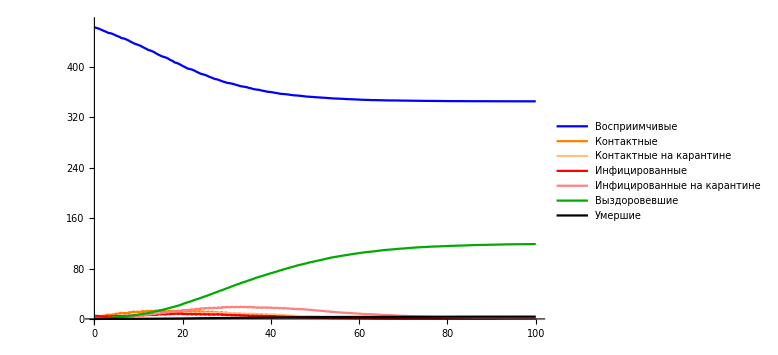

```mathematica
SEIRDQplot[seirdq1hn5mtr10p,16,10]
```

Уровень тестирования от населения - 10%, время ввода меры - через неделю от начала.

```mathematica
seirdq1hn5mtr10p7d=Import[FileNameJoin[{NotebookDirectory[],"seirdq1hn5mtr10p7d.m"}]];
(*seirdq1hn5mtr10p7d=SEIRDmod[DA[up1h5m⟦1⟧,16 100],
DA[up1h5m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,0.1,16,15+16 6,100];*)
```

#### График

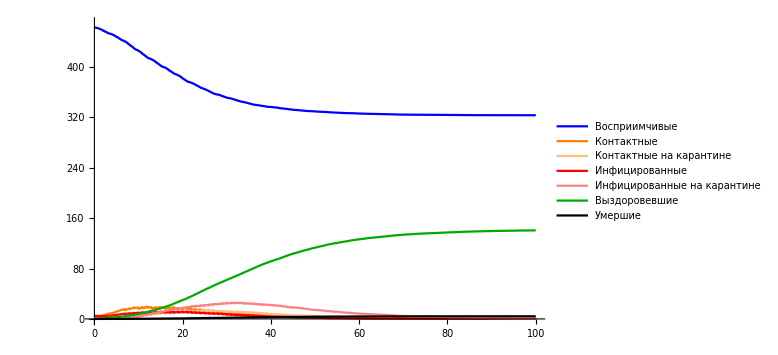

```mathematica
SEIRDQplot[seirdq1hn5mtr10p7d,16,10]
```

Уровень тестирования от населения - 10%, время ввода меры - через две недели от начала.

```mathematica
seirdq1hn5mtr10p14d=Import[FileNameJoin[{NotebookDirectory[],"seirdq1hn5mtr10p14d.m"}]];
(*seirdq1hn5mtr10p14d=SEIRDmod[DA[up1h5m⟦1⟧,16 100],
DA[up1h5m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,0.1,16,15+16 13,100];*)
```

#### График

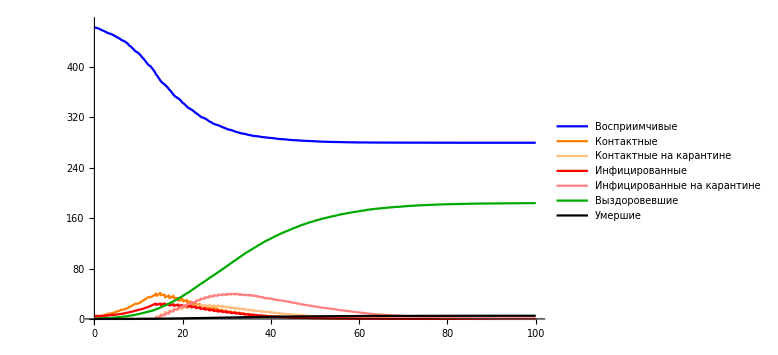

```mathematica
SEIRDQplot[seirdq1hn5mtr10p14d,16,10]
```

Уровень тестирования от населения - 10%, время ввода меры - через три недели от начала.

```mathematica
seirdq1hn5mtr10p21d=Import[FileNameJoin[{NotebookDirectory[],"seirdq1hn5mtr10p21d.m"}]];
(*seirdq1hn5mtr10p21d=SEIRDmod[DA[up1h5m⟦1⟧,16 100],
DA[up1h5m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,0.1,16,15+16 20,100];*)
```

#### График

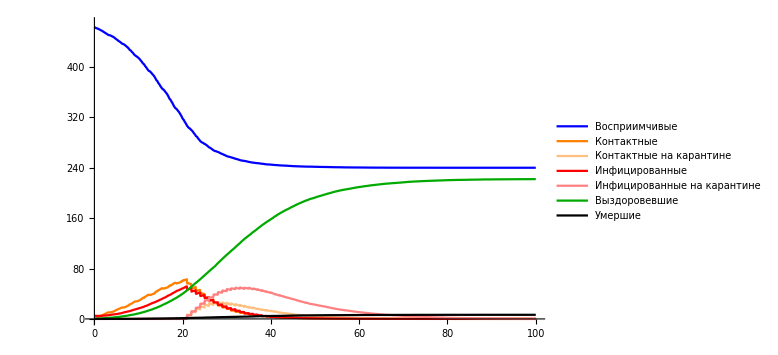

```mathematica
SEIRDQplot[seirdq1hn5mtr10p21d,16,10]
```

#### Наложение графиков

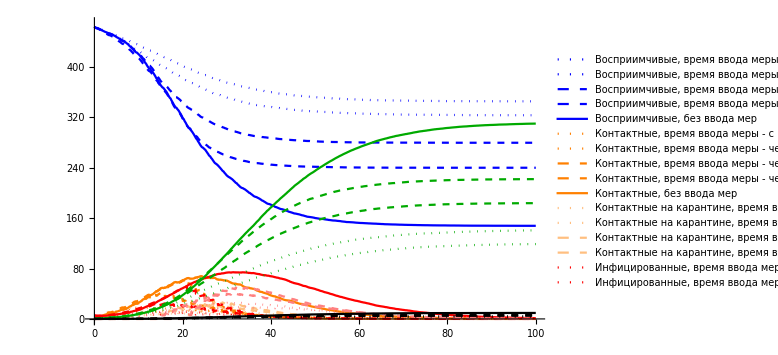

```mathematica
SEIRDQplotsum[seirdq1hn5mtr10p,seirdq1hn5mtr10p7d,seirdq1hn5mtr10p14d,
seirdq1hn5mtr10p21d,seird1hn5m,16,10]
```

Уровень тестирования от населения - 20%, время ввода меры - с первого дня.

```mathematica
seirdq1hn5mtr20p=Import[FileNameJoin[{NotebookDirectory[],"seirdq1hn5mtr20p.m"}]];
(*seirdq1hn5mtr20p=SEIRDmod[DA[up1h5m⟦1⟧,16 100],
DA[up1h5m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,0.2,16,15,100];*)
```

#### График

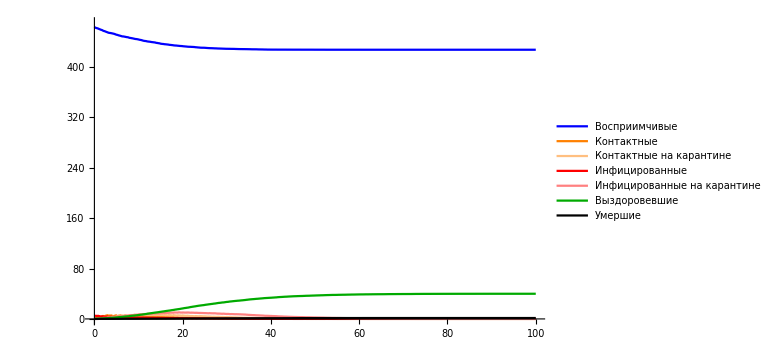

```mathematica
SEIRDQplot[seirdq1hn5mtr20p,16,10]
```

Уровень тестирования от населения - 20%, время ввода меры - через неделю от начала.

```mathematica
seirdq1hn5mtr20p7d=Import[FileNameJoin[{NotebookDirectory[],"seirdq1hn5mtr20p7d.m"}]];
(*seirdq1hn5mtr20p7d=SEIRDmod[DA[up1h5m⟦1⟧,16 100],
DA[up1h5m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,0.2,16,15+16 6,100];*)
```

#### График

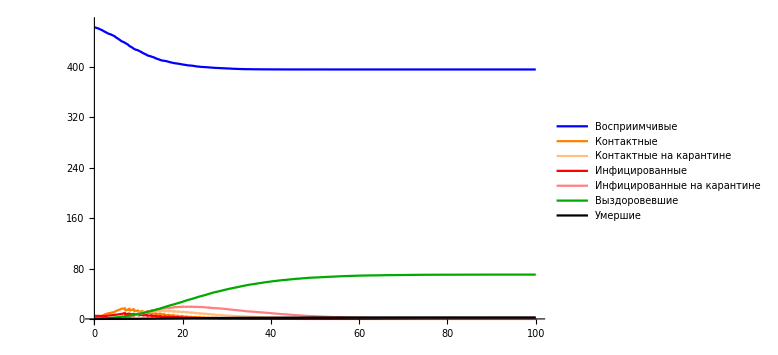

```mathematica
SEIRDQplot[seirdq1hn5mtr20p7d,16,10]
```

Уровень тестирования от населения - 20%, время ввода меры - через две недели от начала.

```mathematica
seirdq1hn5mtr20p14d=Import[FileNameJoin[{NotebookDirectory[],"seirdq1hn5mtr20p14d.m"}]];
(*seirdq1hn5mtr20p14d=SEIRDmod[DA[up1h5m⟦1⟧,16 100],
DA[up1h5m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,0.2,16,15+16 13,100];*)
```

#### График

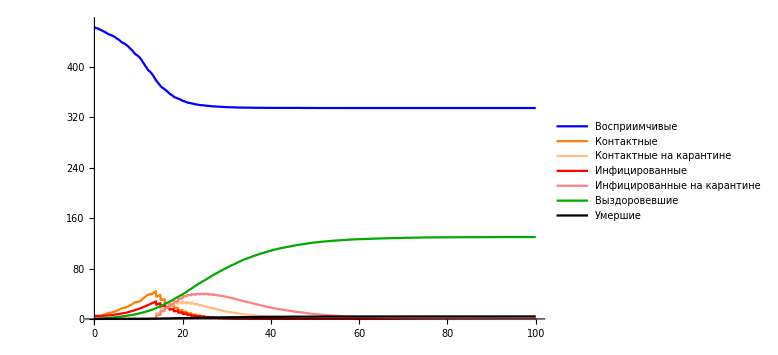

```mathematica
SEIRDQplot[seirdq1hn5mtr20p14d,16,10]
```

Уровень тестирования от населения - 20%, время ввода меры - через три недели от начала.

```mathematica
seirdq1hn5mtr20p21d=Import[FileNameJoin[{NotebookDirectory[],"seirdq1hn5mtr20p21d.m"}]];
(*seirdq1hn5mtr20p21d=SEIRDmod[DA[up1h5m⟦1⟧,16 100],
DA[up1h5m⟦2⟧,16 100],vertexcount,5,1,ϵ1h,γ1h,0.03,0.2,16,15+16 20,100];*)
```

#### График

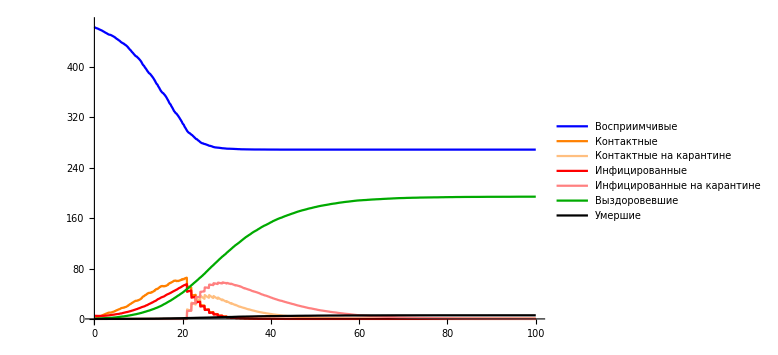

```mathematica
SEIRDQplot[seirdq1hn5mtr20p21d,16,10]
```

#### Наложение графиков

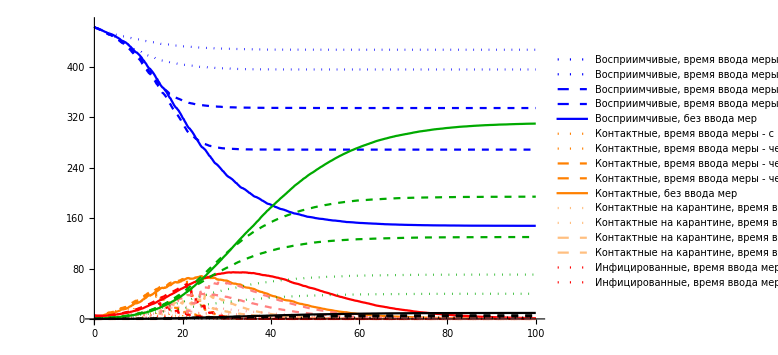

```mathematica
SEIRDQplotsum[seirdq1hn5mtr20p,seirdq1hn5mtr20p7d,seirdq1hn5mtr20p14d,
seirdq1hn5mtr20p21d,seird1hn5m,16,10]
```

## Итоги

## Ссылки

[1] https://github.com/skissler/haslemere
[2] UK Office for National Statistics, “2011 Census summaries for towns and villages in Waverly”, tech. rep., 2011.
[3] Centers for Disease Control and Prevention, “How Flu Spreads,” 2014.
[4] http://crm.ics.org.ru/uploads/crmissues/crm_2012_2/12216.pdf
[5] ???
[6] Kermack, W. O.; McKendrick, A. G. (1927). “A Contribution to the Mathematical Theory of Epidemics”. Proceedings of the Royal Society of London. Series A, Containing Papers of a Mathematical and Physical Character. 115 (772): 700-721.
[7] https://www.bmj.com/content/370/bmj.m3223